### PARAMETRES

```mathematica
ClearAll
listH ={100,100,100} (*мощности слоев*)
slope = 10 Degree (*наклон слоев*)
len = 1000(*длина профиля*)
dx = 5(*шаг по профилю*)
hDispersion = 50(*степень складчатости нижнего слоя в метрах*)
hTapering =5  (*степень влияния нижнего горизонта на верхние*)
listV = {1000,1000,1000, 1000} (*набор скоростей*)
wellCount= 10 (*кол скважин*)
wellType = "max" (*расположение скважин "max","min","regular","random"*)
type = 1 (*выполаживание. 1 - кверху, -1 - книзу*)
```

ClearAll

{100,100,100}

10 °

1000

5

50

5

{1000,1000,1000,1000}

10

max

1

```mathematica
velocityTrend = 0(*1 or 0*)
velocityAnomaly =0 (*1 or 0*)
```

0

0

### DEPTH

```mathematica
horizons = BuildDepthSection[listH,slope,len,dx,hDispersion,hTapering, type][["horizons"]]
```

{{{0,-161},{5,-156},{10,-150},{15,-145},{20,-140},{25,-135},{30,-130},{35,-126},{40,-122},{45,-118},{50,-114},{55,-111},{60,-108},{65,-105},{70,-103},{75,-102},{80,-101},{85,-100},{90,-98},{95,-98},{100,-98},{105,-97},{110,-97},{115,-98},{120,-99},{125,-101},{130,-101},{135,-101},{140,-102},{145,-103},{150,-103},{155,-104},{160,-104},{165,-104},{170,-103},{175,-103},{180,-101},{185,-101},{190,-100},{195,-99},{200,-97},{205,-96},{210,-94},{215,-93},{220,-91},{225,-90},{230,-88},{235,-86},{240,-84},{245,-83},{250,-81},{255,-80},{260,-79},{265,-78},{270,-77},{275,-76},{280,-75},{285,-75},{290,-74},{295,-74},{300,-73},{305,-73},{310,-73},{315,-73},{320,-72},{325,-71},{330,-71},{335,-71},{340,-71},{345,-71},{350,-70},{355,-69},{360,-69},{365,-68},{370,-68},{375,-66},{380,-65},{385,-64},{390,-63},{395,-61},{400,-60},{405,-59},{410,-58},{415,-57},{420,-55},{425,-53},{430,-52},{435,-51},{440,-49},{445,-48},{450,-46},{455,-45},{460,-44},{465,-43},{470,-43},{475,-42},{480,-41},{485,-40},{490,-39},{495,-39},{500,-39},{505,-39},{510,-39},{515,-39},{520,-39},{525,-39},{530,-39},{535,-39},{540,-38},{545,-39},{550,-38},{555,-39},{560,-39},{565,-40},{570,-40},{575,-40},{580,-40},{585,-41},{590,-41},{595,-42},{600,-41},{605,-41},{610,-41},{615,-41},{620,-41},{625,-40},{630,-41},{635,-40},{640,-40},{645,-40},{650,-39},{655,-38},{660,-37},{665,-36},{670,-35},{675,-34},{680,-34},{685,-32},{690,-31},{695,-29},{700,-28},{705,-26},{710,-24},{715,-22},{720,-20},{725,-19},{730,-17},{735,-16},{740,-14},{745,-13},{750,-11},{755,-10},{760,-8},{765,-6},{770,-3},{775,-2},{780,-1},{785,1},{790,3},{795,5},{800,7},{805,8},{810,10},{815,11},{820,13},{825,15},{830,16},{835,19},{840,20},{845,22},{850,24},{855,25},{860,27},{865,28},{870,29},{875,31},{880,32},{885,34},{890,34},{895,34},{900,35},{905,37},{910,38},{915,39},{920,40},{925,41},{930,43},{935,45},{940,47},{945,48},{950,50},{955,52},{960,54},{965,56},{970,58},{975,60},{980,63},{985,66},{990,69},{995,71},{1000,74}},{{0,-282},{5,-275},{10,-268},{15,-260},{20,-253},{25,-245},{30,-239},{35,-232},{40,-226},{45,-221},{50,-216},{55,-212},{60,-208},{65,-205},{70,-203},{75,-202},{80,-202},{85,-202},{90,-203},{95,-203},{100,-205},{105,-207},{110,-209},{115,-212},{120,-215},{125,-217},{130,-220},{135,-222},{140,-224},{145,-225},{150,-227},{155,-228},{160,-229},{165,-227},{170,-226},{175,-225},{180,-223},{185,-221},{190,-219},{195,-217},{200,-215},{205,-213},{210,-210},{215,-207},{220,-206},{225,-204},{230,-202},{235,-199},{240,-197},{245,-194},{250,-193},{255,-191},{260,-190},{265,-188},{270,-187},{275,-186},{280,-186},{285,-185},{290,-185},{295,-185},{300,-186},{305,-188},{310,-188},{315,-189},{320,-189},{325,-190},{330,-190},{335,-190},{340,-190},{345,-189},{350,-189},{355,-187},{360,-186},{365,-185},{370,-184},{375,-182},{380,-181},{385,-180},{390,-178},{395,-177},{400,-177},{405,-176},{410,-175},{415,-174},{420,-172},{425,-171},{430,-169},{435,-167},{440,-165},{445,-164},{450,-161},{455,-159},{460,-156},{465,-155},{470,-153},{475,-151},{480,-149},{485,-149},{490,-148},{495,-149},{500,-149},{505,-150},{510,-151},{515,-152},{520,-153},{525,-154},{530,-154},{535,-155},{540,-155},{545,-156},{550,-157},{555,-157},{560,-157},{565,-157},{570,-157},{575,-156},{580,-156},{585,-155},{590,-155},{595,-155},{600,-154},{605,-155},{610,-155},{615,-155},{620,-155},{625,-155},{630,-156},{635,-156},{640,-156},{645,-157},{650,-158},{655,-159},{660,-158},{665,-159},{670,-157},{675,-157},{680,-155},{685,-153},{690,-150},{695,-148},{700,-145},{705,-142},{710,-140},{715,-137},{720,-134},{725,-131},{730,-128},{735,-126},{740,-124},{745,-123},{750,-122},{755,-120},{760,-120},{765,-119},{770,-120},{775,-119},{780,-119},{785,-117},{790,-117},{795,-117},{800,-114},{805,-112},{810,-110},{815,-108},{820,-105},{825,-101},{830,-98},{835,-95},{840,-91},{845,-87},{850,-85},{855,-83},{860,-81},{865,-79},{870,-78},{875,-78},{880,-78},{885,-79},{890,-80},{895,-80},{900,-81},{905,-81},{910,-82},{915,-82},{920,-81},{925,-80},{930,-79},{935,-77},{940,-75},{945,-73},{950,-70},{955,-67},{960,-65},{965,-62},{970,-59},{975,-57},{980,-53},{985,-50},{990,-47},{995,-43},{1000,-40}},{{0,-394},{5,-385},{10,-377},{15,-368},{20,-359},{25,-350},{30,-342},{35,-335},{40,-328},{45,-323},{50,-318},{55,-315},{60,-312},{65,-309},{70,-308},{75,-307},{80,-306},{85,-306},{90,-307},{95,-308},{100,-309},{105,-311},{110,-314},{115,-317},{120,-320},{125,-325},{130,-329},{135,-333},{140,-335},{145,-339},{150,-339},{155,-339},{160,-339},{165,-339},{170,-337},{175,-335},{180,-333},{185,-329},{190,-326},{195,-323},{200,-320},{205,-319},{210,-317},{215,-316},{220,-314},{225,-312},{230,-309},{235,-307},{240,-305},{245,-303},{250,-300},{255,-298},{260,-296},{265,-294},{270,-291},{275,-290},{280,-289},{285,-290},{290,-291},{295,-291},{300,-293},{305,-294},{310,-295},{315,-297},{320,-298},{325,-299},{330,-301},{335,-302},{340,-301},{345,-300},{350,-298},{355,-297},{360,-294},{365,-292},{370,-290},{375,-288},{380,-286},{385,-285},{390,-283},{395,-283},{400,-283},{405,-282},{410,-283},{415,-283},{420,-284},{425,-283},{430,-281},{435,-278},{440,-275},{445,-272},{450,-269},{455,-265},{460,-262},{465,-259},{470,-256},{475,-253},{480,-253},{485,-253},{490,-252},{495,-254},{500,-255},{505,-257},{510,-259},{515,-260},{520,-261},{525,-262},{530,-264},{535,-265},{540,-265},{545,-265},{550,-266},{555,-265},{560,-265},{565,-265},{570,-264},{575,-264},{580,-264},{585,-263},{590,-262},{595,-263},{600,-261},{605,-261},{610,-261},{615,-261},{620,-261},{625,-261},{630,-262},{635,-263},{640,-264},{645,-266},{650,-267},{655,-267},{660,-268},{665,-269},{670,-269},{675,-267},{680,-266},{685,-264},{690,-262},{695,-258},{700,-254},{705,-251},{710,-246},{715,-242},{720,-238},{725,-235},{730,-234},{735,-231},{740,-229},{745,-228},{750,-227},{755,-227},{760,-227},{765,-227},{770,-226},{775,-227},{780,-227},{785,-227},{790,-226},{795,-226},{800,-225},{805,-224},{810,-222},{815,-220},{820,-215},{825,-212},{830,-208},{835,-203},{840,-198},{845,-193},{850,-188},{855,-184},{860,-181},{865,-180},{870,-180},{875,-181},{880,-182},{885,-184},{890,-187},{895,-189},{900,-192},{905,-194},{910,-194},{915,-194},{920,-193},{925,-192},{930,-188},{935,-185},{940,-182},{945,-180},{950,-177},{955,-175},{960,-172},{965,-170},{970,-167},{975,-165},{980,-162},{985,-160},{990,-157},{995,-153},{1000,-149}},{{0,-528},{5,-517},{10,-504},{15,-491},{20,-477},{25,-464},{30,-453},{35,-445},{40,-438},{45,-433},{50,-431},{55,-430},{60,-430},{65,-430},{70,-429},{75,-430},{80,-429},{85,-428},{90,-427},{95,-428},{100,-426},{105,-424},{110,-424},{115,-427},{120,-435},{125,-443},{130,-454},{135,-464},{140,-470},{145,-472},{150,-472},{155,-471},{160,-471},{165,-471},{170,-471},{175,-466},{180,-457},{185,-445},{190,-435},{195,-429},{200,-429},{205,-435},{210,-443},{215,-449},{220,-450},{225,-443},{230,-435},{235,-427},{240,-423},{245,-422},{250,-422},{255,-420},{260,-418},{265,-414},{270,-408},{275,-405},{280,-405},{285,-406},{290,-409},{295,-411},{300,-413},{305,-415},{310,-418},{315,-419},{320,-422},{325,-424},{330,-426},{335,-428},{340,-430},{345,-431},{350,-429},{355,-426},{360,-422},{365,-416},{370,-411},{375,-406},{380,-401},{385,-398},{390,-395},{395,-395},{400,-398},{405,-403},{410,-408},{415,-412},{420,-415},{425,-416},{430,-412},{435,-409},{440,-404},{445,-400},{450,-395},{455,-390},{460,-385},{465,-377},{470,-367},{475,-357},{480,-353},{485,-357},{490,-364},{495,-376},{500,-385},{505,-394},{510,-396},{515,-391},{520,-387},{525,-383},{530,-379},{535,-378},{540,-380},{545,-385},{550,-391},{555,-397},{560,-398},{565,-398},{570,-393},{575,-386},{580,-379},{585,-375},{590,-375},{595,-379},{600,-383},{605,-388},{610,-392},{615,-391},{620,-389},{625,-383},{630,-377},{635,-374},{640,-374},{645,-378},{650,-384},{655,-393},{660,-401},{665,-404},{670,-405},{675,-400},{680,-397},{685,-392},{690,-388},{695,-381},{700,-374},{705,-372},{710,-367},{715,-363},{720,-357},{725,-353},{730,-350},{735,-346},{740,-343},{745,-342},{750,-343},{755,-347},{760,-349},{765,-354},{770,-357},{775,-357},{780,-352},{785,-348},{790,-345},{795,-343},{800,-345},{805,-346},{810,-348},{815,-350},{820,-350},{825,-347},{830,-343},{835,-336},{840,-325},{845,-313},{850,-302},{855,-291},{860,-285},{865,-281},{870,-283},{875,-289},{880,-296},{885,-301},{890,-309},{895,-318},{900,-327},{905,-334},{910,-339},{915,-338},{920,-331},{925,-318},{930,-305},{935,-297},{940,-292},{945,-291},{950,-294},{955,-296},{960,-296},{965,-295},{970,-293},{975,-292},{980,-290},{985,-288},{990,-286},{995,-281},{1000,-274}}}

```mathematica
PlotDepthSection[horizons, Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]]
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
PlotVelocity[velModel, horizons, {PlotStyle -> {Directive[Thickness[0.005], Black]},
							PlotLabel->"Velocity Distribution",
							PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
							ImageSize -> 500, 
ColorFunction -> ColorData[{"RedBlueTones", "Reverse"}],
						PlotLegends -> BarLegend[Automatic, LegendLabel -> "Vel, m/s"],
						PlotLabel -> "Velocity Distribution",
						Contours -> {Automatic, 20}}]
```

-Graphics-

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]]
```

{{{0,0},{5,0},{10,0},{15,0},{20,0},{25,0},{30,0},{35,0},{40,0},{45,0},{50,0},{55,0},{60,0},{65,0},{70,0},{75,0},{80,0},{85,0},{90,0},{95,0},{100,0},{105,0},{110,0},{115,0},{120,0},{125,0},{130,0},{135,0},{140,0},{145,0},{150,0},{155,0},{160,0},{165,0},{170,0},{175,0},{180,0},{185,0},{190,0},{195,0},{200,0},{205,0},{210,0},{215,0},{220,0},{225,0},{230,0},{235,0},{240,0},{245,0},{250,0},{255,0},{260,0},{265,0},{270,0},{275,0},{280,0},{285,0},{290,0},{295,0},{300,0},{305,0},{310,0},{315,0},{320,0},{325,0},{330,0},{335,0},{340,0},{345,0},{350,0},{355,0},{360,0},{365,0},{370,0},{375,0},{380,0},{385,0},{390,0},{395,0},{400,0},{405,0},{410,0},{415,0},{420,0},{425,0},{430,0},{435,0},{440,0},{445,0},{450,0},{455,0},{460,0},{465,0},{470,0},{475,0},{480,0},{485,0},{490,0},{495,0},{500,0},{505,0},{510,0},{515,0},{520,0},{525,0},{530,0},{535,0},{540,0},{545,0},{550,0},{555,0},{560,0},{565,0},{570,0},{575,0},{580,0},{585,0},{590,0},{595,0},{600,0},{605,0},{610,0},{615,0},{620,0},{625,0},{630,0},{635,0},{640,0},{645,0},{650,0},{655,0},{660,0},{665,0},{670,0},{675,0},{680,0},{685,0},{690,0},{695,0},{700,0},{705,0},{710,0},{715,0},{720,0},{725,0},{730,0},{735,0},{740,0},{745,0},{750,0},{755,0},{760,0},{765,0},{770,0},{775,0},{780,0},{785,0},{790,0},{795,0},{800,0},{805,0},{810,0},{815,0},{820,0},{825,0},{830,0},{835,0},{840,0},{845,0},{850,0},{855,0},{860,0},{865,0},{870,0},{875,0},{880,0},{885,0},{890,0},{895,0},{900,0},{905,0},{910,0},{915,0},{920,0},{925,0},{930,0},{935,0},{940,0},{945,0},{950,0},{955,0},{960,0},{965,0},{970,0},{975,0},{980,0},{985,0},{990,0},{995,0},{1000,0}},{{0,0.886},{5,0.862},{10,0.836},{15,0.81},{20,0.786},{25,0.76},{30,0.738},{35,0.716},{40,0.696},{45,0.678},{50,0.66},{55,0.646},{60,0.632},{65,0.62},{70,0.612},{75,0.608},{80,0.606},{85,0.604},{90,0.602},{95,0.602},{100,0.606},{105,0.608},{110,0.612},{115,0.62},{120,0.628},{125,0.636},{130,0.642},{135,0.646},{140,0.652},{145,0.656},{150,0.66},{155,0.664},{160,0.666},{165,0.662},{170,0.658},{175,0.656},{180,0.648},{185,0.644},{190,0.638},{195,0.632},{200,0.624},{205,0.618},{210,0.608},{215,0.6},{220,0.594},{225,0.588},{230,0.58},{235,0.57},{240,0.562},{245,0.554},{250,0.548},{255,0.542},{260,0.538},{265,0.532},{270,0.528},{275,0.524},{280,0.522},{285,0.52},{290,0.518},{295,0.518},{300,0.518},{305,0.522},{310,0.522},{315,0.524},{320,0.522},{325,0.522},{330,0.522},{335,0.522},{340,0.522},{345,0.52},{350,0.518},{355,0.512},{360,0.51},{365,0.506},{370,0.504},{375,0.496},{380,0.492},{385,0.488},{390,0.482},{395,0.476},{400,0.474},{405,0.47},{410,0.466},{415,0.462},{420,0.454},{425,0.448},{430,0.442},{435,0.436},{440,0.428},{445,0.424},{450,0.414},{455,0.408},{460,0.4},{465,0.396},{470,0.392},{475,0.386},{480,0.38},{485,0.378},{490,0.374},{495,0.376},{500,0.376},{505,0.378},{510,0.38},{515,0.382},{520,0.384},{525,0.386},{530,0.386},{535,0.388},{540,0.386},{545,0.39},{550,0.39},{555,0.392},{560,0.392},{565,0.394},{570,0.394},{575,0.392},{580,0.392},{585,0.392},{590,0.392},{595,0.394},{600,0.39},{605,0.392},{610,0.392},{615,0.392},{620,0.392},{625,0.39},{630,0.394},{635,0.392},{640,0.392},{645,0.394},{650,0.394},{655,0.394},{660,0.39},{665,0.39},{670,0.384},{675,0.382},{680,0.378},{685,0.37},{690,0.362},{695,0.354},{700,0.346},{705,0.336},{710,0.328},{715,0.318},{720,0.308},{725,0.3},{730,0.29},{735,0.284},{740,0.276},{745,0.272},{750,0.266},{755,0.26},{760,0.256},{765,0.25},{770,0.246},{775,0.242},{780,0.24},{785,0.236},{790,0.24},{795,0.244},{800,0.242},{805,0.24},{810,0.24},{815,0.238},{820,0.236},{825,0.232},{830,0.228},{835,0.228},{840,0.222},{845,0.218},{850,0.218},{855,0.216},{860,0.216},{865,0.214},{870,0.214},{875,0.218},{880,0.22},{885,0.226},{890,0.228},{895,0.228},{900,0.232},{905,0.236},{910,0.24},{915,0.242},{920,0.242},{925,0.242},{930,0.244},{935,0.244},{940,0.244},{945,0.242},{950,0.24},{955,0.238},{960,0.238},{965,0.236},{970,0.234},{975,0.234},{980,0.232},{985,0.232},{990,0.232},{995,0.228},{1000,0.228}},{{0,1.674},{5,1.632},{10,1.59},{15,1.546},{20,1.504},{25,1.46},{30,1.422},{35,1.386},{40,1.352},{45,1.324},{50,1.296},{55,1.276},{60,1.256},{65,1.238},{70,1.228},{75,1.222},{80,1.218},{85,1.216},{90,1.216},{95,1.218},{100,1.224},{105,1.23},{110,1.24},{115,1.254},{120,1.268},{125,1.286},{130,1.3},{135,1.312},{140,1.322},{145,1.334},{150,1.338},{155,1.342},{160,1.344},{165,1.34},{170,1.332},{175,1.326},{180,1.314},{185,1.302},{190,1.29},{195,1.278},{200,1.264},{205,1.256},{210,1.242},{215,1.232},{220,1.222},{225,1.212},{230,1.198},{235,1.184},{240,1.172},{245,1.16},{250,1.148},{255,1.138},{260,1.13},{265,1.12},{270,1.11},{275,1.104},{280,1.1},{285,1.1},{290,1.1},{295,1.1},{300,1.104},{305,1.11},{310,1.112},{315,1.118},{320,1.118},{325,1.12},{330,1.124},{335,1.126},{340,1.124},{345,1.12},{350,1.114},{355,1.106},{360,1.098},{365,1.09},{370,1.084},{375,1.072},{380,1.064},{385,1.058},{390,1.048},{395,1.042},{400,1.04},{405,1.034},{410,1.032},{415,1.028},{420,1.022},{425,1.014},{430,1.004},{435,0.992},{440,0.978},{445,0.968},{450,0.952},{455,0.938},{460,0.924},{465,0.914},{470,0.904},{475,0.892},{480,0.886},{485,0.884},{490,0.878},{495,0.884},{500,0.886},{505,0.892},{510,0.898},{515,0.902},{520,0.906},{525,0.91},{530,0.914},{535,0.918},{540,0.916},{545,0.92},{550,0.922},{555,0.922},{560,0.922},{565,0.924},{570,0.922},{575,0.92},{580,0.92},{585,0.918},{590,0.916},{595,0.92},{600,0.912},{605,0.914},{610,0.914},{615,0.914},{620,0.914},{625,0.912},{630,0.918},{635,0.918},{640,0.92},{645,0.926},{650,0.928},{655,0.928},{660,0.926},{665,0.928},{670,0.922},{675,0.916},{680,0.91},{685,0.898},{690,0.886},{695,0.87},{700,0.854},{705,0.838},{710,0.82},{715,0.802},{720,0.784},{725,0.77},{730,0.758},{735,0.746},{740,0.734},{745,0.728},{750,0.72},{755,0.714},{760,0.71},{765,0.704},{770,0.698},{775,0.696},{780,0.694},{785,0.69},{790,0.692},{795,0.696},{800,0.692},{805,0.688},{810,0.684},{815,0.678},{820,0.666},{825,0.656},{830,0.644},{835,0.634},{840,0.618},{845,0.604},{850,0.594},{855,0.584},{860,0.578},{865,0.574},{870,0.574},{875,0.58},{880,0.584},{885,0.594},{890,0.602},{895,0.606},{900,0.616},{905,0.624},{910,0.628},{915,0.63},{920,0.628},{925,0.626},{930,0.62},{935,0.614},{940,0.608},{945,0.602},{950,0.594},{955,0.588},{960,0.582},{965,0.576},{970,0.568},{975,0.564},{980,0.556},{985,0.552},{990,0.546},{995,0.534},{1000,0.526}},{{0,2.73},{5,2.666},{10,2.598},{15,2.528},{20,2.458},{25,2.388},{30,2.328},{35,2.276},{40,2.228},{45,2.19},{50,2.158},{55,2.136},{60,2.116},{65,2.098},{70,2.086},{75,2.082},{80,2.076},{85,2.072},{90,2.07},{95,2.074},{100,2.076},{105,2.078},{110,2.088},{115,2.108},{120,2.138},{125,2.172},{130,2.208},{135,2.24},{140,2.262},{145,2.278},{150,2.282},{155,2.284},{160,2.286},{165,2.282},{170,2.274},{175,2.258},{180,2.228},{185,2.192},{190,2.16},{195,2.136},{200,2.122},{205,2.126},{210,2.128},{215,2.13},{220,2.122},{225,2.098},{230,2.068},{235,2.038},{240,2.018},{245,2.004},{250,1.992},{255,1.978},{260,1.966},{265,1.948},{270,1.926},{275,1.914},{280,1.91},{285,1.912},{290,1.918},{295,1.922},{300,1.93},{305,1.94},{310,1.948},{315,1.956},{320,1.962},{325,1.968},{330,1.976},{335,1.982},{340,1.984},{345,1.982},{350,1.972},{355,1.958},{360,1.942},{365,1.922},{370,1.906},{375,1.884},{380,1.866},{385,1.854},{390,1.838},{395,1.832},{400,1.836},{405,1.84},{410,1.848},{415,1.852},{420,1.852},{425,1.846},{430,1.828},{435,1.81},{440,1.786},{445,1.768},{450,1.742},{455,1.718},{460,1.694},{465,1.668},{470,1.638},{475,1.606},{480,1.592},{485,1.598},{490,1.606},{495,1.636},{500,1.656},{505,1.68},{510,1.69},{515,1.684},{520,1.68},{525,1.676},{530,1.672},{535,1.674},{540,1.676},{545,1.69},{550,1.704},{555,1.716},{560,1.718},{565,1.72},{570,1.708},{575,1.692},{580,1.678},{585,1.668},{590,1.666},{595,1.678},{600,1.678},{605,1.69},{610,1.698},{615,1.696},{620,1.692},{625,1.678},{630,1.672},{635,1.666},{640,1.668},{645,1.682},{650,1.696},{655,1.714},{660,1.728},{665,1.736},{670,1.732},{675,1.716},{680,1.704},{685,1.682},{690,1.662},{695,1.632},{700,1.602},{705,1.582},{710,1.554},{715,1.528},{720,1.498},{725,1.476},{730,1.458},{735,1.438},{740,1.42},{745,1.412},{750,1.406},{755,1.408},{760,1.408},{765,1.412},{770,1.412},{775,1.41},{780,1.398},{785,1.386},{790,1.382},{795,1.382},{800,1.382},{805,1.38},{810,1.38},{815,1.378},{820,1.366},{825,1.35},{830,1.33},{835,1.306},{840,1.268},{845,1.23},{850,1.198},{855,1.166},{860,1.148},{865,1.136},{870,1.14},{875,1.158},{880,1.176},{885,1.196},{890,1.22},{895,1.242},{900,1.27},{905,1.292},{910,1.306},{915,1.306},{920,1.29},{925,1.262},{930,1.23},{935,1.208},{940,1.192},{945,1.184},{950,1.182},{955,1.18},{960,1.174},{965,1.166},{970,1.154},{975,1.148},{980,1.136},{985,1.128},{990,1.118},{995,1.096},{1000,1.074}}}

```mathematica
PlotTimeSection[time, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"}]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]]
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]]
```

{200,280,485,540,590,640,750,800,870,1005}

```mathematica
PlotDepthSection[horizons, wellDataset,{GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
											Filling -> Bottom, Frame -> True, ImageSize -> 500,
											PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

```mathematica
Clear[t]
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]]
resultHT=HTMethod[wellDataset, time, t][["result"]]
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]]
```

{FittedModel[-4.18552-175.71 t],FittedModel[-58.7534-106.229 t],FittedModel[-120.875-74.0021 t]}

{{-4.18552,-175.71},{-58.7534,-106.229},{-120.875,-74.0021}}

{{{105,-97.},{195,-99.},{275,-76.},{395,-61.},{480,-41.},{585,-41.},{635,-40.},{745,-13.},{865,28.},{1000,74.}},{{0,-325.661},{5,-315.429},{10,-304.586},{15,-293.833},{20,-283.871},{25,-273.293},{30,-264.205},{35,-255.2},{40,-246.978},{45,-239.537},{50,-232.174},{55,-226.291},{60,-220.481},{65,-215.444},{70,-211.883},{75,-209.794},{80,-208.474},{85,-207.217},{90,-206.021},{95,-205.587},{100,-206.617},{105,-207.},{110,-208.139},{115,-210.736},{120,-213.383},{125,-216.077},{130,-218.115},{135,-219.494},{140,-221.619},{145,-223.08},{150,-224.58},{155,-226.117},{160,-226.985},{165,-225.777},{170,-224.6},{175,-224.155},{180,-221.628},{185,-220.531},{190,-218.755},{195,-217.},{200,-214.561},{205,-212.842},{210,-209.733},{215,-207.34},{220,-205.662},{225,-203.993},{230,-201.628},{235,-198.567},{240,-196.212},{245,-193.86},{250,-192.21},{255,-190.558},{260,-189.604},{265,-187.943},{270,-186.976},{275,-186.},{280,-185.715},{285,-185.417},{290,-185.103},{295,-185.476},{300,-185.834},{305,-187.585},{310,-187.918},{315,-188.943},{320,-188.554},{325,-188.86},{330,-189.16},{335,-189.456},{340,-189.748},{345,-189.336},{350,-188.924},{355,-187.107},{360,-186.698},{365,-185.591},{370,-185.192},{375,-182.692},{380,-181.606},{385,-180.529},{390,-178.76},{395,-177.},{400,-176.653},{405,-175.608},{410,-174.568},{415,-173.53},{420,-171.087},{425,-169.346},{430,-167.603},{435,-165.856},{440,-163.401},{445,-162.345},{450,-159.172},{455,-157.394},{460,-154.901},{465,-153.801},{470,-152.686},{475,-150.852},{480,-149.},{485,-148.534},{490,-147.344},{495,-148.241},{500,-148.416},{505,-149.275},{510,-150.115},{515,-150.94},{520,-151.748},{525,-152.542},{530,-152.619},{535,-153.386},{540,-152.737},{545,-154.185},{550,-154.219},{555,-154.947},{560,-154.965},{565,-155.679},{570,-155.686},{575,-154.987},{580,-154.992},{585,-155.},{590,-155.015},{595,-155.744},{600,-154.377},{605,-155.136},{610,-155.211},{615,-155.31},{620,-155.435},{625,-154.887},{630,-156.48},{635,-156.},{640,-156.262},{645,-157.27},{650,-157.62},{655,-158.019},{660,-157.063},{665,-157.556},{670,-155.975},{675,-155.827},{680,-154.994},{685,-152.765},{690,-150.538},{695,-148.303},{700,-146.053},{705,-143.076},{710,-140.769},{715,-137.718},{720,-134.618},{725,-132.163},{730,-128.939},{735,-127.045},{740,-124.366},{745,-123.},{750,-120.832},{755,-118.559},{760,-116.888},{765,-114.416},{770,-112.552},{775,-110.596},{780,-109.256},{785,-107.127},{790,-107.729},{795,-108.252},{800,-106.592},{805,-104.86},{810,-103.763},{815,-101.898},{820,-99.9716},{825,-97.2839},{830,-94.5412},{835,-93.1524},{840,-89.6068},{845,-86.7189},{850,-85.195},{855,-82.9297},{860,-81.3322},{865,-79.},{870,-77.3421},{875,-77.0647},{880,-76.0626},{885,-76.4476},{890,-75.4116},{895,-73.6608},{900,-73.3071},{905,-72.9481},{910,-72.587},{915,-71.5244},{920,-69.7636},{925,-68.0107},{930,-66.9718},{935,-65.2447},{940,-63.5354},{945,-61.1445},{950,-58.778},{955,-56.4393},{960,-54.8346},{965,-52.5615},{970,-50.3261},{975,-48.8345},{980,-46.6845},{985,-45.285},{990,-43.9365},{995,-41.2366},{1000,-40.}},{{0,-410.037},{5,-400.669},{10,-391.325},{15,-381.581},{20,-372.286},{25,-362.59},{30,-354.191},{35,-346.24},{40,-338.736},{45,-332.529},{50,-326.343},{55,-321.877},{60,-317.433},{65,-313.433},{70,-311.152},{75,-309.741},{80,-308.773},{85,-308.249},{90,-308.167},{95,-308.528},{100,-309.756},{105,-311.},{110,-313.11},{115,-316.086},{120,-319.078},{125,-322.933},{130,-325.954},{135,-328.564},{140,-330.762},{145,-333.399},{150,-334.348},{155,-335.31},{160,-335.859},{165,-335.144},{170,-333.591},{175,-332.473},{180,-330.091},{185,-327.718},{190,-325.355},{195,-323.},{200,-320.229},{205,-318.74},{210,-315.985},{215,-314.086},{220,-312.194},{225,-310.308},{230,-307.579},{235,-304.854},{240,-302.56},{245,-300.27},{250,-297.984},{255,-296.127},{260,-294.697},{265,-292.846},{270,-290.997},{275,-290.},{280,-289.429},{285,-289.709},{290,-289.99},{295,-290.271},{300,-291.402},{305,-292.956},{310,-293.661},{315,-295.213},{320,-295.489},{325,-296.188},{330,-297.309},{335,-298.002},{340,-297.842},{345,-297.253},{350,-296.236},{355,-294.788},{360,-293.336},{365,-291.878},{370,-290.84},{375,-288.521},{380,-287.044},{385,-285.986},{390,-284.071},{395,-283.},{400,-282.773},{405,-281.691},{410,-281.454},{415,-280.789},{420,-279.696},{425,-278.176},{430,-276.23},{435,-273.857},{440,-271.06},{445,-269.112},{450,-265.891},{455,-263.097},{460,-260.305},{465,-258.366},{470,-256.431},{475,-254.076},{480,-253.},{485,-252.78},{490,-251.717},{495,-253.208},{500,-253.853},{505,-255.349},{510,-256.845},{515,-257.913},{520,-258.976},{525,-260.032},{530,-261.08},{535,-262.117},{540,-261.866},{545,-262.876},{550,-263.443},{555,-263.567},{560,-263.67},{565,-264.175},{570,-263.806},{575,-263.413},{580,-263.427},{585,-263.},{590,-262.562},{595,-263.391},{600,-261.667},{605,-262.069},{610,-262.049},{615,-262.038},{620,-262.038},{625,-261.629},{630,-262.94},{635,-263.},{640,-263.512},{645,-264.906},{650,-265.484},{655,-265.677},{660,-265.487},{665,-266.183},{670,-265.21},{675,-264.262},{680,-263.332},{685,-261.14},{690,-258.953},{695,-255.916},{700,-252.873},{705,-249.817},{710,-246.318},{715,-242.794},{720,-239.238},{725,-236.495},{730,-234.133},{735,-231.722},{740,-229.255},{745,-228.},{750,-226.252},{755,-224.858},{760,-223.821},{765,-222.292},{770,-220.701},{775,-219.899},{780,-219.039},{785,-217.699},{790,-217.582},{795,-217.84},{800,-216.352},{805,-214.821},{810,-213.248},{815,-211.212},{820,-207.865},{825,-204.911},{830,-201.502},{835,-198.49},{840,-194.179},{845,-190.271},{850,-187.194},{855,-184.1},{860,-181.843},{865,-180.},{870,-178.999},{875,-179.267},{880,-179.108},{885,-180.224},{890,-180.918},{895,-180.768},{900,-181.902},{905,-182.621},{910,-182.505},{915,-181.981},{920,-180.627},{925,-179.295},{930,-177.138},{935,-175.009},{940,-172.911},{945,-170.846},{950,-168.392},{955,-166.403},{960,-164.454},{965,-162.551},{970,-160.269},{975,-158.887},{980,-156.708},{985,-155.435},{990,-153.795},{995,-150.941},{1000,-149.}},{{0,-572.647},{5,-559.016},{10,-544.987},{15,-530.85},{20,-516.898},{25,-503.126},{30,-491.011},{35,-480.253},{40,-470.256},{45,-461.904},{50,-454.601},{55,-448.934},{60,-443.717},{65,-438.944},{70,-435.204},{75,-432.79},{80,-430.216},{85,-428.071},{90,-426.352},{95,-425.646},{100,-424.764},{105,-424.},{110,-424.533},{115,-426.655},{120,-430.363},{125,-434.763},{130,-439.557},{135,-443.853},{140,-446.757},{145,-448.859},{150,-449.266},{155,-449.455},{160,-449.717},{165,-449.16},{170,-448.077},{175,-445.871},{180,-441.651},{185,-436.597},{190,-432.183},{195,-429.},{200,-427.338},{205,-428.378},{210,-429.156},{215,-429.963},{220,-429.316},{225,-426.323},{230,-422.459},{235,-418.609},{240,-416.25},{245,-414.784},{250,-413.615},{255,-412.149},{260,-410.973},{265,-408.899},{270,-406.218},{275,-405.},{280,-404.944},{285,-405.75},{290,-407.118},{295,-408.157},{300,-409.754},{305,-411.611},{310,-413.136},{315,-414.624},{320,-415.776},{325,-416.887},{330,-418.254},{335,-419.281},{340,-419.673},{345,-419.427},{350,-417.951},{355,-415.836},{360,-413.376},{365,-410.273},{370,-407.711},{375,-404.209},{380,-401.246},{385,-399.115},{390,-396.34},{395,-395.},{400,-395.104},{405,-395.18},{410,-395.828},{415,-395.872},{420,-395.322},{425,-393.888},{430,-390.692},{435,-387.517},{440,-383.484},{445,-380.378},{450,-376.134},{455,-372.241},{460,-368.411},{465,-364.356},{470,-359.789},{475,-355.015},{480,-353.},{485,-354.05},{490,-355.508},{495,-360.329},{500,-363.762},{505,-367.868},{510,-369.967},{515,-369.752},{520,-369.872},{525,-370.017},{530,-370.175},{535,-371.221},{540,-372.251},{545,-375.03},{550,-377.768},{555,-380.154},{560,-380.993},{565,-381.749},{570,-380.34},{575,-378.245},{580,-376.363},{585,-375.},{590,-374.757},{595,-376.533},{600,-376.488},{605,-378.186},{610,-379.267},{615,-378.854},{620,-378.141},{625,-375.953},{630,-374.964},{635,-374.},{640,-374.255},{645,-376.331},{650,-378.461},{655,-381.248},{660,-383.514},{665,-384.957},{670,-384.678},{675,-382.668},{680,-381.286},{685,-378.45},{690,-375.926},{695,-371.928},{700,-367.926},{705,-365.392},{710,-361.65},{715,-358.173},{720,-354.061},{725,-351.081},{730,-348.631},{735,-345.814},{740,-343.213},{745,-342.},{750,-340.983},{755,-341.046},{760,-340.714},{765,-340.88},{770,-340.368},{775,-339.478},{780,-337.032},{785,-334.516},{790,-333.121},{795,-332.26},{800,-331.346},{805,-330.091},{810,-329.091},{815,-327.761},{820,-324.922},{825,-321.468},{830,-317.406},{835,-312.741},{840,-305.998},{845,-299.257},{850,-293.41},{855,-287.575},{860,-283.831},{865,-281.},{870,-280.567},{875,-282.242},{880,-283.959},{885,-286.019},{890,-288.726},{895,-291.196},{900,-294.62},{905,-297.226},{910,-298.727},{915,-298.238},{920,-295.47},{925,-291.021},{930,-286.08},{935,-282.726},{940,-280.373},{945,-279.322},{950,-279.284},{955,-279.375},{960,-279.011},{965,-278.492},{970,-277.529},{975,-277.608},{980,-276.958},{985,-277.066},{990,-277.049},{995,-275.433},{1000,-274.}}}

{{{1.216,-207.},{1.264,-217.},{1.048,-186.},{0.952,-177.},{0.76,-149.},{0.784,-155.},{0.784,-156.},{0.544,-123.},{0.428,-79.},{0.456,-40.}},{{2.46,-311.},{2.556,-323.},{2.208,-290.},{2.084,-283.},{1.772,-253.},{1.836,-263.},{1.836,-263.},{1.456,-228.},{1.148,-180.},{1.052,-149.}},{{4.156,-424.},{4.272,-429.},{3.828,-405.},{3.664,-395.},{3.184,-353.},{3.336,-375.},{3.332,-374.},{2.824,-342.},{2.272,-281.},{2.148,-274.}}}

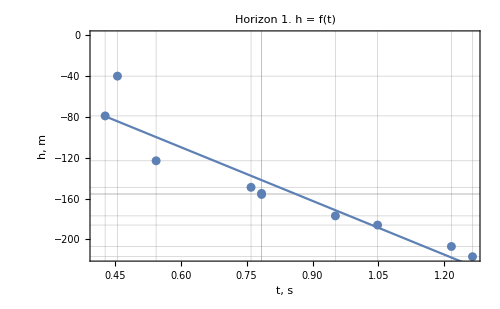
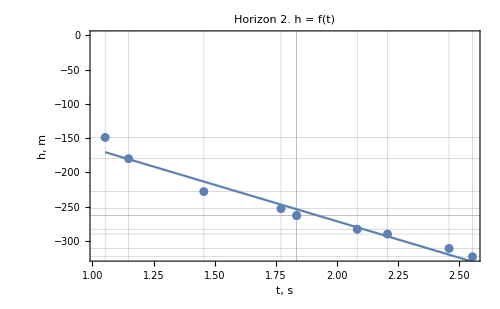
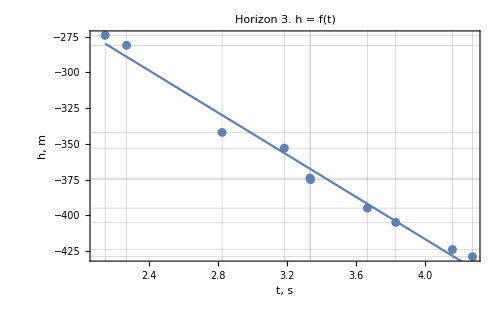

```mathematica
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

```mathematica
lmSetVT=VTMethod[wellDataset,datasetVelModel,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,datasetVelModel,time, t][["lmParametres"]]
wellValuesVT=VTMethod[wellDataset,datasetVelModel,time, t][["wellValues"]]
resultVT = VTMethod[wellDataset,datasetVelModel,time, t][["result"]]
fits = VTMethod[wellDataset,datasetVelModel,time, t][["fits"]]
```

{FittedModel[1000.-1.38652×10^-12 t],FittedModel[1000.+2.27394×10^-13 t],FittedModel[1000.-6.81014×10^-13 t]}

{{1000.,-1.38652×10^-12},{1000.,2.27394×10^-13},{1000.,-6.81014×10^-13}}

{{{1,1.216,1000},{1,1.264,1000},{1,1.048,1000},{1,0.952,1000},{1,0.76,1000},{1,0.784,1000},{1,0.784,1000},{1,0.544,1000},{1,0.428,1000},{1,0.456,1000}},{{2,2.46,1000},{2,2.556,1000},{2,2.208,1000},{2,2.084,1000},{2,1.772,1000},{2,1.836,1000},{2,1.836,1000},{2,1.456,1000},{2,1.148,1000},{2,1.052,1000}},{{3,4.156,1000},{3,4.272,1000},{3,3.828,1000},{3,3.664,1000},{3,3.184,1000},{3,3.336,1000},{3,3.332,1000},{3,2.824,1000},{3,2.272,1000},{3,2.148,1000}}}

{{{105,-97.},{195,-99.},{275,-76.},{395,-61.},{480,-41.},{585,-41.},{635,-40.},{745,-13.},{865,28.},{1000,74.}},{{0,-1882.22},{5,-1742.09},{10,-1602.48},{15,-1467.28},{20,-1340.4},{25,-1213.73},{30,-1099.17},{35,-988.624},{40,-885.997},{45,-791.187},{50,-700.093},{55,-620.618},{60,-544.661},{65,-476.123},{70,-418.906},{75,-372.909},{80,-334.033},{85,-298.179},{90,-265.249},{95,-239.141},{100,-223.758},{105,-207.},{110,-196.767},{115,-196.961},{120,-199.481},{125,-204.23},{130,-207.106},{135,-208.012},{140,-214.847},{145,-219.513},{150,-225.91},{155,-233.939},{160,-239.5},{165,-234.495},{170,-230.824},{175,-232.387},{180,-223.085},{185,-222.82},{190,-219.491},{195,-217.},{200,-211.247},{205,-210.133},{210,-201.558},{215,-197.423},{220,-197.63},{225,-198.078},{230,-194.668},{235,-187.301},{240,-183.878},{245,-180.3},{250,-180.466},{255,-180.279},{260,-183.637},{265,-182.444},{270,-184.597},{275,-186.},{280,-190.552},{285,-194.154},{290,-196.708},{295,-202.194},{300,-206.718},{305,-218.393},{310,-221.332},{315,-227.651},{320,-225.463},{325,-226.882},{330,-228.023},{335,-229.},{340,-229.927},{345,-226.918},{350,-224.087},{355,-213.549},{360,-211.417},{365,-205.806},{370,-204.83},{375,-192.603},{380,-189.239},{385,-186.851},{390,-181.47},{395,-177.},{400,-181.335},{405,-182.367},{410,-183.99},{415,-186.098},{420,-180.583},{425,-179.339},{430,-178.259},{435,-177.236},{440,-172.164},{445,-174.935},{450,-165.444},{455,-163.583},{460,-157.246},{465,-158.326},{470,-158.716},{475,-154.31},{480,-149.},{485,-150.68},{490,-147.253},{495,-154.73},{500,-157.191},{505,-162.719},{510,-167.396},{515,-171.304},{520,-174.526},{525,-177.143},{530,-175.238},{535,-176.893},{540,-170.19},{545,-175.211},{550,-172.038},{555,-172.754},{560,-169.441},{565,-170.18},{570,-167.053},{575,-160.118},{580,-157.418},{585,-155.},{590,-152.907},{595,-155.182},{600,-145.872},{605,-149.019},{610,-148.668},{615,-148.864},{620,-149.651},{625,-147.073},{630,-157.175},{635,-156.},{640,-159.593},{645,-167.999},{650,-173.262},{655,-179.425},{660,-178.512},{665,-186.457},{670,-183.173},{675,-188.572},{680,-190.567},{685,-185.071},{690,-179.996},{695,-175.255},{700,-170.761},{705,-162.426},{710,-158.163},{715,-149.884},{720,-141.503},{725,-136.932},{730,-128.083},{735,-126.87},{740,-121.205},{745,-123.},{750,-120.169},{755,-116.665},{760,-116.502},{765,-111.699},{770,-110.275},{775,-108.25},{780,-109.643},{785,-106.473},{790,-118.76},{795,-130.523},{800,-129.781},{805,-128.554},{810,-130.861},{815,-128.721},{820,-126.154},{825,-119.178},{830,-111.814},{835,-112.08},{840,-99.9963},{845,-91.5815},{850,-90.8551},{855,-85.8366},{860,-84.5451},{865,-79.},{870,-77.2206},{875,-83.2263},{880,-85.0363},{885,-94.67},{890,-96.1466},{895,-93.4856},{900,-98.7061},{905,-103.828},{910,-108.869},{915,-109.851},{920,-106.791},{925,-103.709},{930,-104.625},{935,-101.557},{940,-98.5262},{945,-91.5504},{950,-84.6494},{955,-77.8424},{960,-75.1488},{965,-68.5879},{970,-62.1791},{975,-59.9416},{980,-53.8947},{985,-52.0578},{990,-50.4502},{995,-41.0911},{1000,-40.}},{{0,-3245.15},{5,-2993.17},{10,-2749.39},{15,-2509.64},{20,-2281.72},{25,-2057.46},{30,-1852.68},{35,-1659.2},{40,-1476.83},{45,-1313.4},{50,-1156.72},{55,-1022.61},{60,-894.886},{65,-777.372},{70,-681.886},{75,-600.245},{80,-528.269},{85,-465.775},{90,-412.582},{95,-368.51},{100,-337.376},{105,-311.},{110,-297.2},{115,-295.794},{120,-298.602},{125,-313.442},{130,-324.132},{135,-334.492},{140,-344.34},{145,-361.494},{150,-365.773},{155,-372.997},{160,-378.983},{165,-375.549},{170,-366.516},{175,-363.702},{180,-350.924},{185,-340.002},{190,-330.754},{195,-323.},{200,-312.557},{205,-315.245},{210,-306.881},{215,-307.286},{220,-308.276},{225,-309.672},{230,-303.291},{235,-296.952},{240,-294.474},{245,-291.676},{250,-288.376},{255,-288.392},{260,-291.544},{265,-289.651},{270,-286.53},{275,-290.},{280,-295.88},{285,-307.99},{290,-318.149},{295,-326.325},{300,-340.714},{305,-357.531},{310,-364.988},{315,-379.303},{320,-380.688},{325,-385.358},{330,-393.529},{335,-397.414},{340,-393.228},{345,-385.187},{350,-373.503},{355,-358.392},{360,-344.069},{365,-330.748},{370,-322.644},{375,-303.971},{380,-294.943},{385,-291.774},{390,-282.52},{395,-283.},{400,-293.013},{405,-296.357},{410,-308.83},{415,-318.23},{420,-324.355},{425,-327.005},{430,-325.976},{435,-321.067},{440,-312.077},{445,-310.803},{450,-297.044},{455,-286.598},{460,-275.263},{465,-270.838},{470,-265.12},{475,-253.908},{480,-253.},{485,-258.194},{490,-253.307},{495,-270.365},{500,-277.528},{505,-290.96},{510,-302.825},{515,-309.286},{520,-314.507},{525,-318.65},{530,-321.88},{535,-324.36},{540,-314.254},{545,-315.724},{550,-312.935},{555,-306.05},{560,-299.232},{565,-296.644},{570,-286.446},{575,-276.734},{580,-271.566},{585,-263.},{590,-255.092},{595,-259.9},{600,-241.481},{605,-243.892},{610,-243.191},{615,-243.434},{620,-244.68},{625,-242.984},{630,-258.405},{635,-263.},{640,-272.825},{645,-291.939},{650,-304.398},{655,-314.259},{660,-321.552},{665,-338.187},{670,-340.049},{675,-343.022},{680,-346.989},{685,-339.833},{690,-333.437},{695,-319.687},{700,-306.464},{705,-293.653},{710,-277.137},{715,-260.799},{720,-244.523},{725,-236.193},{730,-231.693},{735,-226.904},{740,-221.712},{745,-228.},{750,-229.652},{755,-234.601},{760,-242.856},{765,-246.434},{770,-249.351},{775,-259.621},{780,-269.261},{785,-274.286},{790,-290.713},{795,-310.557},{800,-313.833},{805,-316.559},{810,-318.748},{815,-316.418},{820,-301.584},{825,-290.262},{830,-274.467},{835,-262.216},{840,-237.523},{845,-216.406},{850,-202.879},{855,-188.958},{860,-182.66},{865,-180.},{870,-184.994},{875,-201.657},{880,-214.005},{885,-238.055},{890,-257.821},{895,-269.32},{900,-292.568},{905,-311.58},{910,-322.372},{915,-328.96},{920,-327.359},{925,-325.586},{930,-315.655},{935,-305.584},{940,-295.388},{945,-285.082},{950,-270.682},{955,-260.204},{960,-249.664},{965,-239.078},{970,-224.461},{975,-217.829},{980,-203.198},{985,-196.584},{990,-186.003},{995,-163.469},{1000,-149.}},{{0,-4510.15},{5,-4153.31},{10,-3799.68},{15,-3453.02},{20,-3117.07},{25,-2791.6},{30,-2496.34},{35,-2227.04},{40,-1975.47},{45,-1753.37},{50,-1552.48},{55,-1380.57},{60,-1221.38},{65,-1074.66},{70,-948.166},{75,-845.644},{80,-746.847},{85,-659.524},{90,-583.428},{95,-526.308},{100,-471.915},{105,-424.},{110,-398.313},{115,-398.606},{120,-424.628},{125,-464.131},{130,-512.865},{135,-558.581},{140,-589.029},{145,-611.96},{150,-615.126},{155,-618.276},{160,-625.161},{165,-623.532},{170,-617.139},{175,-597.734},{180,-553.067},{185,-498.889},{190,-454.949},{195,-429.},{200,-424.791},{205,-458.074},{210,-488.599},{215,-520.116},{220,-532.377},{225,-513.132},{230,-482.131},{235,-451.126},{240,-439.867},{245,-440.104},{250,-443.59},{255,-442.073},{260,-443.305},{265,-431.036},{270,-409.018},{275,-405.},{280,-414.734},{285,-433.97},{290,-458.462},{295,-476.177},{300,-499.406},{305,-524.473},{310,-543.698},{315,-561.404},{320,-573.911},{325,-585.541},{330,-600.616},{335,-611.458},{340,-614.387},{345,-609.726},{350,-589.796},{355,-562.919},{360,-533.416},{365,-497.609},{370,-471.819},{375,-436.368},{380,-411.578},{385,-401.766},{390,-387.007},{395,-395.},{400,-425.412},{405,-457.909},{410,-500.159},{415,-535.828},{420,-564.582},{425,-582.089},{430,-576.014},{435,-570.026},{440,-551.79},{445,-544.974},{450,-521.243},{455,-500.265},{460,-477.706},{465,-449.234},{470,-410.514},{475,-365.214},{480,-353.},{485,-377.539},{490,-402.529},{495,-468.032},{500,-510.345},{505,-557.769},{510,-574.605},{515,-557.153},{520,-541.716},{525,-524.592},{530,-506.084},{535,-498.493},{540,-490.119},{545,-505.262},{550,-520.225},{555,-531.308},{560,-522.811},{565,-515.036},{570,-480.271},{575,-438.651},{580,-402.216},{585,-375.},{590,-365.041},{595,-384.376},{600,-381.041},{605,-403.072},{610,-418.506},{615,-415.379},{620,-409.729},{625,-385.591},{630,-379.003},{635,-374.},{640,-386.619},{645,-424.898},{650,-464.871},{655,-514.577},{660,-558.024},{665,-591.119},{670,-601.74},{675,-589.767},{680,-587.079},{685,-565.554},{690,-549.072},{695,-513.512},{700,-478.753},{705,-464.673},{710,-435.153},{715,-410.07},{720,-377.305},{725,-360.735},{730,-352.241},{735,-339.701},{740,-330.994},{745,-342.},{750,-356.598},{755,-386.71},{760,-412.325},{765,-445.437},{770,-470.041},{775,-490.129},{780,-489.697},{785,-488.739},{790,-503.248},{795,-525.219},{800,-546.645},{805,-563.522},{810,-583.843},{815,-599.602},{820,-594.793},{825,-581.411},{830,-559.449},{835,-528.902},{840,-469.764},{845,-410.029},{850,-361.691},{855,-312.744},{860,-291.182},{865,-281.},{870,-302.191},{875,-350.75},{880,-398.671},{885,-449.947},{890,-508.574},{895,-562.544},{900,-627.853},{905,-680.494},{910,-716.462},{915,-723.75},{920,-698.353},{925,-648.265},{930,-589.48},{935,-549.991},{940,-521.794},{945,-508.882},{950,-507.25},{955,-504.891},{960,-493.8},{965,-477.971},{970,-453.397},{975,-440.074},{980,-413.994},{985,-395.153},{990,-371.544},{995,-323.162},{1000,-274.}}}

{{{0,-1772.},{5,-1724.},{10,-1672.},{15,-1620.},{20,-1572.},{25,-1520.},{30,-1476.},{35,-1432.},{40,-1392.},{45,-1356.},{50,-1320.},{55,-1292.},{60,-1264.},{65,-1240.},{70,-1224.},{75,-1216.},{80,-1212.},{85,-1208.},{90,-1204.},{95,-1204.},{100,-1212.},{105,-1216.},{110,-1224.},{115,-1240.},{120,-1256.},{125,-1272.},{130,-1284.},{135,-1292.},{140,-1304.},{145,-1312.},{150,-1320.},{155,-1328.},{160,-1332.},{165,-1324.},{170,-1316.},{175,-1312.},{180,-1296.},{185,-1288.},{190,-1276.},{195,-1264.},{200,-1248.},{205,-1236.},{210,-1216.},{215,-1200.},{220,-1188.},{225,-1176.},{230,-1160.},{235,-1140.},{240,-1124.},{245,-1108.},{250,-1096.},{255,-1084.},{260,-1076.},{265,-1064.},{270,-1056.},{275,-1048.},{280,-1044.},{285,-1040.},{290,-1036.},{295,-1036.},{300,-1036.},{305,-1044.},{310,-1044.},{315,-1048.},{320,-1044.},{325,-1044.},{330,-1044.},{335,-1044.},{340,-1044.},{345,-1040.},{350,-1036.},{355,-1024.},{360,-1020.},{365,-1012.},{370,-1008.},{375,-992.},{380,-984.},{385,-976.},{390,-964.},{395,-952.},{400,-948.},{405,-940.},{410,-932.},{415,-924.},{420,-908.},{425,-896.},{430,-884.},{435,-872.},{440,-856.},{445,-848.},{450,-828.},{455,-816.},{460,-800.},{465,-792.},{470,-784.},{475,-772.},{480,-760.},{485,-756.},{490,-748.},{495,-752.},{500,-752.},{505,-756.},{510,-760.},{515,-764.},{520,-768.},{525,-772.},{530,-772.},{535,-776.},{540,-772.},{545,-780.},{550,-780.},{555,-784.},{560,-784.},{565,-788.},{570,-788.},{575,-784.},{580,-784.},{585,-784.},{590,-784.},{595,-788.},{600,-780.},{605,-784.},{610,-784.},{615,-784.},{620,-784.},{625,-780.},{630,-788.},{635,-784.},{640,-784.},{645,-788.},{650,-788.},{655,-788.},{660,-780.},{665,-780.},{670,-768.},{675,-764.},{680,-756.},{685,-740.},{690,-724.},{695,-708.},{700,-692.},{705,-672.},{710,-656.},{715,-636.},{720,-616.},{725,-600.},{730,-580.},{735,-568.},{740,-552.},{745,-544.},{750,-532.},{755,-520.},{760,-512.},{765,-500.},{770,-492.},{775,-484.},{780,-480.},{785,-472.},{790,-480.},{795,-488.},{800,-484.},{805,-480.},{810,-480.},{815,-476.},{820,-472.},{825,-464.},{830,-456.},{835,-456.},{840,-444.},{845,-436.},{850,-436.},{855,-432.},{860,-432.},{865,-428.},{870,-428.},{875,-436.},{880,-440.},{885,-452.},{890,-456.},{895,-456.},{900,-464.},{905,-472.},{910,-480.},{915,-484.},{920,-484.},{925,-484.},{930,-488.},{935,-488.},{940,-488.},{945,-484.},{950,-480.},{955,-476.},{960,-476.},{965,-472.},{970,-468.},{975,-468.},{980,-464.},{985,-464.},{990,-464.},{995,-456.},{1000,-456.}},{{0,-3348.},{5,-3264.},{10,-3180.},{15,-3092.},{20,-3008.},{25,-2920.},{30,-2844.},{35,-2772.},{40,-2704.},{45,-2648.},{50,-2592.},{55,-2552.},{60,-2512.},{65,-2476.},{70,-2456.},{75,-2444.},{80,-2436.},{85,-2432.},{90,-2432.},{95,-2436.},{100,-2448.},{105,-2460.},{110,-2480.},{115,-2508.},{120,-2536.},{125,-2572.},{130,-2600.},{135,-2624.},{140,-2644.},{145,-2668.},{150,-2676.},{155,-2684.},{160,-2688.},{165,-2680.},{170,-2664.},{175,-2652.},{180,-2628.},{185,-2604.},{190,-2580.},{195,-2556.},{200,-2528.},{205,-2512.},{210,-2484.},{215,-2464.},{220,-2444.},{225,-2424.},{230,-2396.},{235,-2368.},{240,-2344.},{245,-2320.},{250,-2296.},{255,-2276.},{260,-2260.},{265,-2240.},{270,-2220.},{275,-2208.},{280,-2200.},{285,-2200.},{290,-2200.},{295,-2200.},{300,-2208.},{305,-2220.},{310,-2224.},{315,-2236.},{320,-2236.},{325,-2240.},{330,-2248.},{335,-2252.},{340,-2248.},{345,-2240.},{350,-2228.},{355,-2212.},{360,-2196.},{365,-2180.},{370,-2168.},{375,-2144.},{380,-2128.},{385,-2116.},{390,-2096.},{395,-2084.},{400,-2080.},{405,-2068.},{410,-2064.},{415,-2056.},{420,-2044.},{425,-2028.},{430,-2008.},{435,-1984.},{440,-1956.},{445,-1936.},{450,-1904.},{455,-1876.},{460,-1848.},{465,-1828.},{470,-1808.},{475,-1784.},{480,-1772.},{485,-1768.},{490,-1756.},{495,-1768.},{500,-1772.},{505,-1784.},{510,-1796.},{515,-1804.},{520,-1812.},{525,-1820.},{530,-1828.},{535,-1836.},{540,-1832.},{545,-1840.},{550,-1844.},{555,-1844.},{560,-1844.},{565,-1848.},{570,-1844.},{575,-1840.},{580,-1840.},{585,-1836.},{590,-1832.},{595,-1840.},{600,-1824.},{605,-1828.},{610,-1828.},{615,-1828.},{620,-1828.},{625,-1824.},{630,-1836.},{635,-1836.},{640,-1840.},{645,-1852.},{650,-1856.},{655,-1856.},{660,-1852.},{665,-1856.},{670,-1844.},{675,-1832.},{680,-1820.},{685,-1796.},{690,-1772.},{695,-1740.},{700,-1708.},{705,-1676.},{710,-1640.},{715,-1604.},{720,-1568.},{725,-1540.},{730,-1516.},{735,-1492.},{740,-1468.},{745,-1456.},{750,-1440.},{755,-1428.},{760,-1420.},{765,-1408.},{770,-1396.},{775,-1392.},{780,-1388.},{785,-1380.},{790,-1384.},{795,-1392.},{800,-1384.},{805,-1376.},{810,-1368.},{815,-1356.},{820,-1332.},{825,-1312.},{830,-1288.},{835,-1268.},{840,-1236.},{845,-1208.},{850,-1188.},{855,-1168.},{860,-1156.},{865,-1148.},{870,-1148.},{875,-1160.},{880,-1168.},{885,-1188.},{890,-1204.},{895,-1212.},{900,-1232.},{905,-1248.},{910,-1256.},{915,-1260.},{920,-1256.},{925,-1252.},{930,-1240.},{935,-1228.},{940,-1216.},{945,-1204.},{950,-1188.},{955,-1176.},{960,-1164.},{965,-1152.},{970,-1136.},{975,-1128.},{980,-1112.},{985,-1104.},{990,-1092.},{995,-1068.},{1000,-1052.}},{{0,-5460.},{5,-5332.},{10,-5196.},{15,-5056.},{20,-4916.},{25,-4776.},{30,-4656.},{35,-4552.},{40,-4456.},{45,-4380.},{50,-4316.},{55,-4272.},{60,-4232.},{65,-4196.},{70,-4172.},{75,-4164.},{80,-4152.},{85,-4144.},{90,-4140.},{95,-4148.},{100,-4152.},{105,-4156.},{110,-4176.},{115,-4216.},{120,-4276.},{125,-4344.},{130,-4416.},{135,-4480.},{140,-4524.},{145,-4556.},{150,-4564.},{155,-4568.},{160,-4572.},{165,-4564.},{170,-4548.},{175,-4516.},{180,-4456.},{185,-4384.},{190,-4320.},{195,-4272.},{200,-4244.},{205,-4252.},{210,-4256.},{215,-4260.},{220,-4244.},{225,-4196.},{230,-4136.},{235,-4076.},{240,-4036.},{245,-4008.},{250,-3984.},{255,-3956.},{260,-3932.},{265,-3896.},{270,-3852.},{275,-3828.},{280,-3820.},{285,-3824.},{290,-3836.},{295,-3844.},{300,-3860.},{305,-3880.},{310,-3896.},{315,-3912.},{320,-3924.},{325,-3936.},{330,-3952.},{335,-3964.},{340,-3968.},{345,-3964.},{350,-3944.},{355,-3916.},{360,-3884.},{365,-3844.},{370,-3812.},{375,-3768.},{380,-3732.},{385,-3708.},{390,-3676.},{395,-3664.},{400,-3672.},{405,-3680.},{410,-3696.},{415,-3704.},{420,-3704.},{425,-3692.},{430,-3656.},{435,-3620.},{440,-3572.},{445,-3536.},{450,-3484.},{455,-3436.},{460,-3388.},{465,-3336.},{470,-3276.},{475,-3212.},{480,-3184.},{485,-3196.},{490,-3212.},{495,-3272.},{500,-3312.},{505,-3360.},{510,-3380.},{515,-3368.},{520,-3360.},{525,-3352.},{530,-3344.},{535,-3348.},{540,-3352.},{545,-3380.},{550,-3408.},{555,-3432.},{560,-3436.},{565,-3440.},{570,-3416.},{575,-3384.},{580,-3356.},{585,-3336.},{590,-3332.},{595,-3356.},{600,-3356.},{605,-3380.},{610,-3396.},{615,-3392.},{620,-3384.},{625,-3356.},{630,-3344.},{635,-3332.},{640,-3336.},{645,-3364.},{650,-3392.},{655,-3428.},{660,-3456.},{665,-3472.},{670,-3464.},{675,-3432.},{680,-3408.},{685,-3364.},{690,-3324.},{695,-3264.},{700,-3204.},{705,-3164.},{710,-3108.},{715,-3056.},{720,-2996.},{725,-2952.},{730,-2916.},{735,-2876.},{740,-2840.},{745,-2824.},{750,-2812.},{755,-2816.},{760,-2816.},{765,-2824.},{770,-2824.},{775,-2820.},{780,-2796.},{785,-2772.},{790,-2764.},{795,-2764.},{800,-2764.},{805,-2760.},{810,-2760.},{815,-2756.},{820,-2732.},{825,-2700.},{830,-2660.},{835,-2612.},{840,-2536.},{845,-2460.},{850,-2396.},{855,-2332.},{860,-2296.},{865,-2272.},{870,-2280.},{875,-2316.},{880,-2352.},{885,-2392.},{890,-2440.},{895,-2484.},{900,-2540.},{905,-2584.},{910,-2612.},{915,-2612.},{920,-2580.},{925,-2524.},{930,-2460.},{935,-2416.},{940,-2384.},{945,-2368.},{950,-2364.},{955,-2360.},{960,-2348.},{965,-2332.},{970,-2308.},{975,-2296.},{980,-2272.},{985,-2256.},{990,-2236.},{995,-2192.},{1000,-2148.}}}

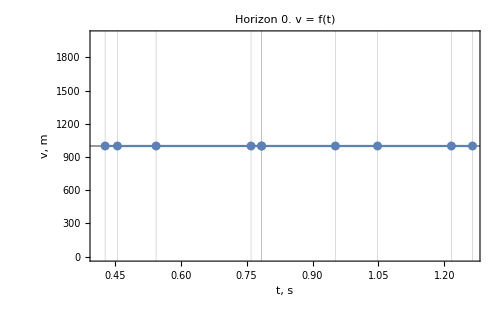
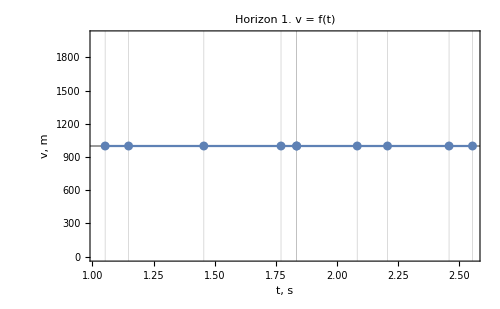
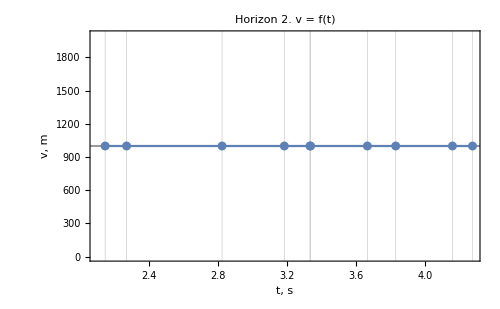

```mathematica
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

```mathematica
Clear[h]
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]]
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]]
resultTH=THMethod[wellDataset, time, h][["result"]]
```

{FittedModel[0.0753074-0.00502547 h],FittedModel[-0.462876-0.00905889 h],FittedModel[-1.54947-0.0132833 h]}

{{0.0753074,-0.00502547},{-0.462876,-0.00905889},{-1.54947,-0.0132833}}

{{{-207.,1.216},{-217.,1.264},{-186.,1.048},{-177.,0.952},{-149.,0.76},{-155.,0.784},{-156.,0.784},{-123.,0.544},{-79.,0.428},{-40.,0.456}},{{-311.,2.46},{-323.,2.556},{-290.,2.208},{-283.,2.084},{-253.,1.772},{-263.,1.836},{-263.,1.836},{-228.,1.456},{-180.,1.148},{-149.,1.052}},{{-424.,4.156},{-429.,4.272},{-405.,3.828},{-395.,3.664},{-353.,3.184},{-375.,3.336},{-374.,3.332},{-342.,2.824},{-281.,2.272},{-274.,2.148}}}

{{{105,-97.},{195,-99.},{275,-76.},{395,-61.},{480,-41.},{585,-41.},{635,-40.},{745,-13.},{865,28.},{1000,74.}},{{0,-369.616},{5,-355.716},{10,-341.236},{15,-326.969},{20,-313.706},{25,-299.849},{30,-287.783},{35,-275.91},{40,-265.023},{45,-255.115},{50,-245.387},{55,-237.426},{60,-229.635},{65,-222.805},{70,-217.729},{75,-214.4},{80,-212.019},{85,-209.785},{90,-207.693},{95,-206.535},{100,-207.101},{105,-207.},{110,-207.818},{115,-210.347},{120,-212.99},{125,-215.743},{130,-217.804},{135,-219.17},{140,-221.427},{145,-222.98},{150,-224.618},{155,-226.338},{160,-227.339},{165,-226.024},{170,-224.776},{175,-224.387},{180,-221.669},{185,-220.596},{190,-218.776},{195,-217.},{200,-214.468},{205,-212.766},{210,-209.502},{215,-207.06},{220,-205.435},{225,-203.826},{230,-201.432},{235,-198.249},{240,-195.864},{245,-193.477},{250,-191.878},{255,-190.267},{260,-189.436},{265,-187.788},{270,-186.909},{275,-186.},{280,-185.852},{285,-185.663},{290,-185.43},{295,-185.948},{300,-186.424},{305,-188.454},{310,-188.861},{315,-190.036},{320,-189.596},{325,-189.934},{330,-190.258},{335,-190.572},{340,-190.883},{345,-190.397},{350,-189.917},{355,-187.853},{360,-187.396},{365,-186.162},{370,-185.747},{375,-182.972},{380,-181.821},{385,-180.708},{390,-178.837},{395,-177.},{400,-176.785},{405,-175.799},{410,-174.834},{415,-173.885},{420,-171.355},{425,-169.628},{430,-167.904},{435,-166.178},{440,-163.649},{445,-162.701},{450,-159.349},{455,-157.569},{460,-154.968},{465,-153.929},{470,-152.857},{475,-150.95},{480,-149.},{485,-148.594},{490,-147.341},{495,-148.425},{500,-148.664},{505,-149.654},{510,-150.603},{515,-151.515},{520,-152.391},{525,-153.236},{530,-153.258},{535,-154.05},{540,-153.23},{545,-154.779},{550,-154.722},{555,-155.45},{560,-155.373},{565,-156.089},{570,-156.007},{575,-155.132},{580,-155.06},{585,-155.},{590,-154.956},{595,-155.728},{600,-154.137},{605,-154.963},{610,-155.027},{615,-155.128},{620,-155.272},{625,-154.666},{630,-156.499},{635,-156.},{640,-156.356},{645,-157.573},{650,-158.062},{655,-158.624},{660,-157.669},{665,-158.372},{670,-156.743},{675,-156.752},{680,-155.999},{685,-153.678},{690,-151.37},{695,-149.064},{700,-146.751},{705,-143.622},{710,-141.26},{715,-138.062},{720,-134.812},{725,-132.298},{730,-128.914},{735,-127.04},{740,-124.276},{745,-123.},{750,-120.813},{755,-118.505},{760,-116.877},{765,-114.339},{770,-112.487},{775,-110.53},{780,-109.267},{785,-107.109},{790,-108.04},{795,-108.881},{800,-107.247},{805,-105.529},{810,-104.528},{815,-102.656},{820,-100.711},{825,-97.9021},{830,-95.0289},{835,-93.6869},{840,-89.9002},{845,-86.8562},{850,-85.3548},{855,-83.0118},{860,-81.4229},{865,-79.},{870,-77.3387},{875,-77.2387},{880,-76.316},{885,-76.9621},{890,-75.9971},{895,-74.2207},{900,-74.0243},{905,-73.8201},{910,-73.6116},{915,-72.6067},{920,-70.8092},{925,-69.0187},{930,-68.0351},{935,-66.2701},{940,-64.5235},{945,-62.0031},{950,-59.5086},{955,-57.0437},{960,-55.4083},{965,-53.014},{970,-50.6608},{975,-49.1482},{980,-46.8881},{985,-45.4763},{990,-44.1205},{995,-41.2325},{1000,-40.}},{{0,-423.232},{5,-412.734},{10,-402.3},{15,-391.485},{20,-381.173},{25,-370.478},{30,-361.165},{35,-352.35},{40,-344.033},{45,-337.094},{50,-330.207},{55,-325.139},{60,-320.12},{65,-315.592},{70,-312.878},{75,-311.093},{80,-309.795},{85,-308.982},{90,-308.653},{95,-308.807},{100,-309.884},{105,-311.},{110,-313.036},{115,-315.992},{120,-318.982},{125,-322.889},{130,-325.946},{135,-328.591},{140,-330.825},{145,-333.529},{150,-334.495},{155,-335.486},{160,-336.06},{165,-335.333},{170,-333.744},{175,-332.619},{180,-330.188},{185,-327.775},{190,-325.38},{195,-323.},{200,-320.193},{205,-318.724},{210,-315.942},{215,-314.055},{220,-312.176},{225,-310.306},{230,-307.559},{235,-304.818},{240,-302.522},{245,-300.23},{250,-297.939},{255,-296.091},{260,-294.683},{265,-292.831},{270,-290.976},{275,-290.},{280,-289.459},{285,-289.794},{290,-290.121},{295,-290.439},{300,-291.631},{305,-293.257},{310,-293.993},{315,-295.604},{320,-295.886},{325,-296.603},{330,-297.757},{335,-298.465},{340,-298.286},{345,-297.663},{350,-296.595},{355,-295.084},{360,-293.572},{365,-292.059},{370,-290.988},{375,-288.592},{380,-287.081},{385,-286.013},{390,-284.064},{395,-283.},{400,-282.82},{405,-281.759},{410,-281.582},{415,-280.963},{420,-279.904},{425,-278.403},{430,-276.461},{435,-274.077},{440,-271.25},{445,-269.306},{450,-266.036},{455,-263.206},{460,-260.375},{465,-258.424},{470,-256.472},{475,-254.075},{480,-253.},{485,-252.805},{490,-251.724},{495,-253.288},{500,-253.963},{505,-255.515},{510,-257.059},{515,-258.152},{520,-259.234},{525,-260.305},{530,-261.363},{535,-262.407},{540,-262.11},{545,-263.122},{550,-263.674},{555,-263.765},{560,-263.836},{565,-264.326},{570,-263.911},{575,-263.475},{580,-263.465},{585,-263.},{590,-262.527},{595,-263.375},{600,-261.574},{605,-261.984},{610,-261.961},{615,-261.951},{620,-261.957},{625,-261.543},{630,-262.919},{635,-263.},{640,-263.555},{645,-265.031},{650,-265.665},{655,-265.903},{660,-265.748},{665,-266.518},{670,-265.559},{675,-264.629},{680,-263.721},{685,-261.506},{690,-259.3},{695,-256.213},{700,-253.122},{705,-250.021},{710,-246.461},{715,-242.877},{720,-239.263},{725,-236.493},{730,-234.122},{735,-231.699},{740,-229.219},{745,-228.},{750,-226.268},{755,-224.904},{760,-223.909},{765,-222.405},{770,-220.834},{775,-220.083},{780,-219.272},{785,-217.962},{790,-217.922},{795,-218.272},{800,-216.806},{805,-215.294},{810,-213.739},{815,-211.701},{820,-208.301},{825,-205.308},{830,-201.841},{835,-198.786},{840,-194.38},{845,-190.392},{850,-187.267},{855,-184.123},{860,-181.847},{865,-180.},{870,-179.027},{875,-179.371},{880,-179.271},{885,-180.493},{890,-181.276},{895,-181.18},{900,-182.417},{905,-183.222},{910,-183.156},{915,-182.665},{920,-181.31},{925,-179.976},{930,-177.783},{935,-175.617},{940,-173.481},{945,-171.378},{950,-168.868},{955,-166.839},{960,-164.851},{965,-162.907},{970,-160.568},{975,-159.162},{980,-156.925},{985,-155.626},{990,-153.944},{995,-150.999},{1000,-149.}},{{0,-578.091},{5,-563.986},{10,-549.487},{15,-534.89},{20,-520.493},{25,-506.29},{30,-493.784},{35,-482.669},{40,-472.337},{45,-463.69},{50,-456.119},{55,-450.222},{60,-444.792},{65,-439.823},{70,-435.914},{75,-433.361},{80,-430.654},{85,-428.392},{90,-426.569},{95,-425.785},{100,-424.829},{105,-424.},{110,-424.497},{115,-426.616},{120,-430.355},{125,-434.804},{130,-439.659},{135,-444.011},{140,-446.954},{145,-449.085},{150,-449.496},{155,-449.688},{160,-449.959},{165,-449.401},{170,-448.311},{175,-446.081},{180,-441.805},{185,-436.683},{190,-432.215},{195,-429.},{200,-427.335},{205,-428.419},{210,-429.238},{215,-430.088},{220,-429.459},{225,-426.443},{230,-422.542},{235,-418.654},{240,-416.282},{245,-414.819},{250,-413.657},{255,-412.191},{260,-411.018},{265,-408.929},{270,-406.222},{275,-405.},{280,-404.957},{285,-405.789},{290,-407.189},{295,-408.251},{300,-409.878},{305,-411.767},{310,-413.317},{315,-414.826},{320,-415.994},{325,-417.121},{330,-418.506},{335,-419.547},{340,-419.942},{345,-419.691},{350,-418.189},{355,-416.039},{360,-413.542},{365,-410.394},{370,-407.8},{375,-404.254},{380,-401.26},{385,-399.119},{390,-396.327},{395,-395.},{400,-395.146},{405,-395.266},{410,-395.972},{415,-396.066},{420,-395.556},{425,-394.148},{430,-390.948},{435,-387.769},{440,-383.717},{445,-380.606},{450,-376.335},{455,-372.418},{460,-368.562},{465,-364.474},{470,-359.86},{475,-355.029},{480,-353.},{485,-354.083},{490,-355.573},{495,-360.477},{500,-363.965},{505,-368.13},{510,-370.25},{515,-370.011},{520,-370.109},{525,-370.231},{530,-370.363},{535,-371.397},{540,-372.414},{545,-375.21},{550,-377.965},{555,-380.363},{560,-381.189},{565,-381.933},{570,-380.478},{575,-378.329},{580,-376.399},{585,-375.},{590,-374.744},{595,-376.544},{600,-376.495},{605,-378.22},{610,-379.322},{615,-378.905},{620,-378.185},{625,-375.966},{630,-374.969},{635,-374.},{640,-374.272},{645,-376.398},{650,-378.581},{655,-381.433},{660,-383.755},{665,-385.242},{670,-384.978},{675,-382.955},{680,-381.571},{685,-378.709},{690,-376.165},{695,-372.123},{700,-368.079},{705,-365.529},{710,-361.752},{715,-358.244},{720,-354.093},{725,-351.094},{730,-348.636},{735,-345.806},{740,-343.196},{745,-342.},{750,-341.005},{755,-341.109},{760,-340.813},{765,-341.025},{770,-340.547},{775,-339.686},{780,-337.243},{785,-334.73},{790,-333.356},{795,-332.527},{800,-331.644},{805,-330.414},{810,-329.443},{815,-328.137},{820,-325.295},{825,-321.828},{830,-317.741},{835,-313.04},{840,-306.225},{845,-299.41},{850,-293.504},{855,-287.61},{860,-283.842},{865,-281.},{870,-280.597},{875,-282.336},{880,-284.117},{885,-286.246},{890,-289.03},{895,-291.571},{900,-295.08},{905,-297.756},{910,-299.304},{915,-298.826},{920,-296.027},{925,-291.515},{930,-286.5},{935,-283.096},{940,-280.707},{945,-279.64},{950,-279.599},{955,-279.687},{960,-279.308},{965,-278.768},{970,-277.773},{975,-277.833},{980,-277.148},{985,-277.229},{990,-277.18},{995,-275.499},{1000,-274.}}}

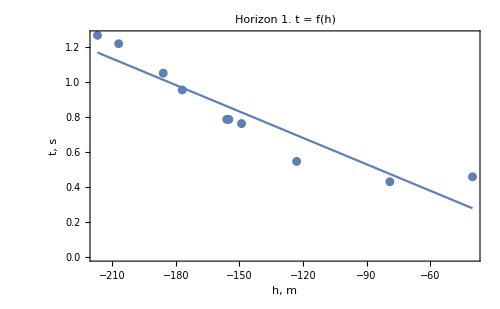
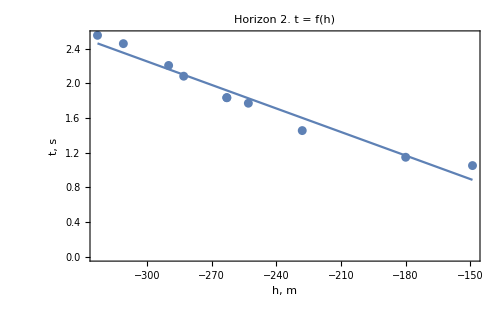
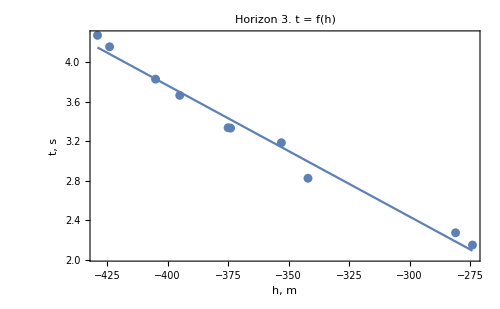

```mathematica
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]]
fits = VaveMethod[wellDataset, time][["fits"]]
```

{179.645,140.422,112.391}

{{{105,-97.},{195,-99.},{275,-76.},{395,-61.},{480,-41.},{585,-41.},{635,-40.},{745,-13.},{865,28.},{1000,74.}},{{0,-333.093},{5,-322.24},{10,-310.782},{15,-299.435},{20,-288.915},{25,-277.783},{30,-268.192},{35,-258.701},{40,-250.029},{45,-242.171},{50,-234.408},{55,-228.173},{60,-222.028},{65,-216.689},{70,-212.871},{75,-210.573},{80,-209.073},{85,-207.651},{90,-206.304},{95,-205.748},{100,-206.699},{105,-207.},{110,-208.085},{115,-210.67},{120,-213.316},{125,-216.021},{130,-218.063},{135,-219.44},{140,-221.586},{145,-223.063},{150,-224.587},{155,-226.154},{160,-227.045},{165,-225.819},{170,-224.63},{175,-224.194},{180,-221.635},{185,-220.542},{190,-218.759},{195,-217.},{200,-214.545},{205,-212.829},{210,-209.694},{215,-207.293},{220,-205.623},{225,-203.964},{230,-201.595},{235,-198.513},{240,-196.154},{245,-193.795},{250,-192.153},{255,-190.508},{260,-189.576},{265,-187.917},{270,-186.965},{275,-186.},{280,-185.738},{285,-185.458},{290,-185.158},{295,-185.556},{300,-185.934},{305,-187.732},{310,-188.077},{315,-189.128},{320,-188.73},{325,-189.042},{330,-189.346},{335,-189.645},{340,-189.94},{345,-189.515},{350,-189.092},{355,-187.233},{360,-186.816},{365,-185.688},{370,-185.286},{375,-182.739},{380,-181.642},{385,-180.559},{390,-178.773},{395,-177.},{400,-176.675},{405,-175.64},{410,-174.613},{415,-173.59},{420,-171.132},{425,-169.394},{430,-167.654},{435,-165.911},{440,-163.443},{445,-162.405},{450,-159.202},{455,-157.423},{460,-154.913},{465,-153.823},{470,-152.715},{475,-150.869},{480,-149.},{485,-148.544},{490,-147.343},{495,-148.272},{500,-148.458},{505,-149.339},{510,-150.198},{515,-151.037},{520,-151.857},{525,-152.659},{530,-152.727},{535,-153.499},{540,-152.82},{545,-154.286},{550,-154.304},{555,-155.032},{560,-155.034},{565,-155.748},{570,-155.74},{575,-155.011},{580,-155.003},{585,-155.},{590,-155.005},{595,-155.741},{600,-154.337},{605,-155.107},{610,-155.18},{615,-155.279},{620,-155.407},{625,-154.849},{630,-156.483},{635,-156.},{640,-156.278},{645,-157.321},{650,-157.695},{655,-158.122},{660,-157.165},{665,-157.694},{670,-156.105},{675,-155.983},{680,-155.164},{685,-152.919},{690,-150.678},{695,-148.432},{700,-146.171},{705,-143.168},{710,-140.852},{715,-137.776},{720,-134.651},{725,-132.186},{730,-128.934},{735,-127.044},{740,-124.35},{745,-123.},{750,-120.828},{755,-118.55},{760,-116.886},{765,-114.403},{770,-112.541},{775,-110.585},{780,-109.257},{785,-107.124},{790,-107.781},{795,-108.358},{800,-106.703},{805,-104.973},{810,-103.892},{815,-102.026},{820,-100.097},{825,-97.3884},{830,-94.6236},{835,-93.2428},{840,-89.6564},{845,-86.7422},{850,-85.222},{855,-82.9436},{860,-81.3475},{865,-79.},{870,-77.3415},{875,-77.0941},{880,-76.1054},{885,-76.5346},{890,-75.5106},{895,-73.7555},{900,-73.4284},{905,-73.0955},{910,-72.7602},{915,-71.7074},{920,-69.9403},{925,-68.1811},{930,-67.1516},{935,-65.418},{940,-63.7025},{945,-61.2896},{950,-58.9015},{955,-56.5415},{960,-54.9316},{965,-52.638},{970,-50.3827},{975,-48.8876},{980,-46.719},{985,-45.3174},{990,-43.9676},{995,-41.2359},{1000,-40.}},{{0,-518.5},{5,-499.85},{10,-481.538},{15,-462.994},{20,-445.335},{25,-427.43},{30,-411.519},{35,-396.47},{40,-382.276},{45,-370.054},{50,-358.11},{55,-348.685},{60,-339.524},{65,-331.182},{70,-325.336},{75,-320.855},{80,-317.17},{85,-314.275},{90,-312.162},{95,-310.823},{100,-310.812},{105,-311.},{110,-312.502},{115,-315.31},{120,-318.294},{125,-322.57},{130,-325.884},{135,-328.791},{140,-331.282},{145,-334.474},{150,-335.551},{155,-336.752},{160,-337.509},{165,-336.69},{170,-334.851},{175,-333.668},{180,-330.888},{185,-328.188},{190,-325.561},{195,-323.},{200,-319.935},{205,-318.607},{210,-315.637},{215,-313.826},{220,-312.044},{225,-310.284},{230,-307.415},{235,-304.552},{240,-302.251},{245,-299.941},{250,-297.616},{255,-295.831},{260,-294.577},{265,-292.724},{270,-290.826},{275,-290.},{280,-289.676},{285,-290.409},{290,-291.067},{295,-291.65},{300,-293.288},{305,-295.427},{310,-296.389},{315,-298.43},{320,-298.749},{325,-299.599},{330,-300.99},{335,-301.805},{340,-301.491},{345,-300.617},{350,-299.192},{355,-297.222},{360,-295.277},{365,-293.365},{370,-292.057},{375,-289.112},{380,-287.347},{385,-286.208},{390,-284.012},{395,-283.},{400,-283.165},{405,-282.252},{410,-282.502},{415,-282.222},{420,-281.405},{425,-280.044},{430,-278.133},{435,-275.663},{440,-272.629},{445,-270.707},{450,-267.083},{455,-263.996},{460,-260.877},{465,-258.843},{470,-256.764},{475,-254.069},{480,-253.},{485,-252.987},{490,-251.777},{495,-253.864},{500,-254.759},{505,-256.712},{510,-258.604},{515,-259.878},{520,-261.1},{525,-262.275},{530,-263.406},{535,-264.498},{540,-263.87},{545,-264.897},{550,-265.337},{555,-265.192},{560,-265.031},{565,-265.417},{570,-264.672},{575,-263.923},{580,-263.738},{585,-263.},{590,-262.276},{595,-263.258},{600,-260.895},{605,-261.373},{610,-261.328},{615,-261.326},{620,-261.374},{625,-260.916},{630,-262.767},{635,-263.},{640,-263.868},{645,-265.94},{650,-266.973},{655,-267.536},{660,-267.632},{665,-268.938},{670,-268.073},{675,-267.275},{680,-266.533},{685,-264.15},{690,-261.802},{695,-258.356},{700,-254.923},{705,-251.494},{710,-247.497},{715,-243.482},{720,-239.44},{725,-236.483},{730,-234.04},{735,-231.538},{740,-228.966},{745,-228.},{750,-226.382},{755,-225.231},{760,-224.549},{765,-223.216},{770,-221.797},{775,-221.418},{780,-220.96},{785,-219.864},{790,-220.38},{795,-221.387},{800,-220.082},{805,-218.713},{810,-217.284},{815,-215.237},{820,-211.451},{825,-208.176},{830,-204.293},{835,-200.928},{840,-195.837},{845,-191.271},{850,-187.794},{855,-184.286},{860,-181.874},{865,-180.},{870,-179.228},{875,-180.124},{880,-180.443},{885,-182.437},{890,-183.86},{895,-184.156},{900,-186.135},{905,-187.555},{910,-187.856},{915,-187.604},{920,-186.24},{925,-184.891},{930,-182.437},{935,-180.005},{940,-177.597},{945,-175.216},{950,-172.306},{955,-169.991},{960,-167.714},{965,-165.478},{970,-162.725},{975,-161.142},{980,-158.487},{985,-157.009},{990,-155.027},{995,-151.42},{1000,-149.}},{{0,-735.885},{5,-708.026},{10,-679.918},{15,-651.995},{20,-624.694},{25,-598.},{30,-574.147},{35,-552.671},{40,-532.658},{45,-515.445},{50,-500.116},{55,-487.557},{60,-475.956},{65,-465.299},{70,-456.47},{75,-449.906},{80,-443.343},{85,-437.667},{90,-432.864},{95,-429.819},{100,-426.719},{105,-424.},{110,-423.446},{115,-425.492},{120,-430.125},{125,-435.981},{130,-442.597},{135,-448.609},{140,-452.655},{145,-455.621},{150,-456.142},{155,-456.454},{160,-456.99},{165,-456.389},{170,-455.086},{175,-452.167},{180,-446.27},{185,-439.179},{190,-433.127},{195,-429.},{200,-427.233},{205,-429.609},{210,-431.62},{215,-433.701},{220,-433.589},{225,-429.922},{230,-424.933},{235,-419.957},{240,-417.229},{245,-415.833},{250,-414.858},{255,-413.39},{260,-412.313},{265,-409.816},{270,-406.334},{275,-405.},{280,-405.35},{285,-406.92},{290,-409.246},{295,-410.977},{300,-413.471},{305,-416.29},{310,-418.549},{315,-420.709},{320,-422.331},{325,-423.879},{330,-425.814},{335,-427.248},{340,-427.745},{345,-427.317},{350,-425.076},{355,-421.934},{360,-418.352},{365,-413.894},{370,-410.369},{375,-405.543},{380,-401.674},{385,-399.225},{390,-395.953},{395,-395.},{400,-396.36},{405,-397.78},{410,-400.153},{415,-401.675},{420,-402.339},{425,-401.69},{430,-398.375},{435,-395.083},{440,-390.462},{445,-387.202},{450,-382.15},{455,-377.548},{460,-372.942},{465,-367.875},{470,-361.892},{475,-355.437},{480,-353.},{485,-355.024},{490,-357.457},{495,-364.794},{500,-369.839},{505,-375.74},{510,-378.451},{515,-377.521},{520,-376.996},{525,-376.425},{530,-375.81},{535,-376.497},{540,-377.138},{545,-380.429},{550,-383.674},{555,-386.421},{560,-386.872},{565,-387.275},{570,-384.482},{575,-380.749},{580,-377.435},{585,-375.},{590,-374.354},{595,-376.858},{600,-376.677},{605,-379.218},{610,-380.894},{615,-380.369},{620,-379.451},{625,-376.352},{630,-375.131},{635,-374.},{640,-374.768},{645,-378.344},{650,-382.044},{655,-386.776},{660,-390.749},{665,-393.504},{670,-393.677},{675,-391.254},{680,-389.818},{685,-386.207},{690,-383.104},{695,-377.797},{700,-372.521},{705,-369.508},{710,-364.698},{715,-360.324},{720,-355.024},{725,-351.481},{730,-348.781},{735,-345.561},{740,-342.706},{745,-342.},{750,-341.63},{755,-342.939},{760,-343.683},{765,-345.215},{770,-345.744},{775,-345.723},{780,-343.361},{785,-340.91},{790,-340.174},{795,-340.259},{800,-340.272},{805,-339.768},{810,-339.652},{815,-339.031},{820,-336.11},{825,-332.245},{830,-327.44},{835,-321.702},{840,-312.787},{845,-303.849},{850,-296.24},{855,-288.619},{860,-284.136},{865,-281.},{870,-281.463},{875,-285.082},{880,-288.714},{885,-292.815},{890,-297.84},{895,-302.445},{900,-308.435},{905,-313.116},{910,-316.045},{915,-315.878},{920,-312.172},{925,-305.831},{930,-298.658},{935,-293.807},{940,-290.382},{945,-288.839},{950,-288.735},{955,-288.725},{960,-287.915},{965,-286.762},{970,-284.82},{975,-284.344},{980,-282.64},{985,-281.962},{990,-280.966},{995,-277.412},{1000,-274.}}}

{{{0,-318.331},{5,-309.708},{10,-300.367},{15,-291.025},{20,-282.402},{25,-273.061},{30,-265.156},{35,-257.252},{40,-250.066},{45,-243.599},{50,-237.131},{55,-232.101},{60,-227.071},{65,-222.76},{70,-219.886},{75,-218.448},{80,-217.73},{85,-217.011},{90,-216.293},{95,-216.293},{100,-217.73},{105,-218.448},{110,-219.886},{115,-222.76},{120,-225.634},{125,-228.509},{130,-230.664},{135,-232.101},{140,-234.257},{145,-235.694},{150,-237.131},{155,-238.569},{160,-239.287},{165,-237.85},{170,-236.413},{175,-235.694},{180,-232.82},{185,-231.383},{190,-229.227},{195,-227.071},{200,-224.197},{205,-222.041},{210,-218.448},{215,-215.574},{220,-213.418},{225,-211.263},{230,-208.388},{235,-204.795},{240,-201.921},{245,-199.047},{250,-196.891},{255,-194.735},{260,-193.298},{265,-191.142},{270,-189.705},{275,-188.268},{280,-187.549},{285,-186.831},{290,-186.112},{295,-186.112},{300,-186.112},{305,-187.549},{310,-187.549},{315,-188.268},{320,-187.549},{325,-187.549},{330,-187.549},{335,-187.549},{340,-187.549},{345,-186.831},{350,-186.112},{355,-183.957},{360,-183.238},{365,-181.801},{370,-181.082},{375,-178.208},{380,-176.771},{385,-175.334},{390,-173.178},{395,-171.022},{400,-170.304},{405,-168.866},{410,-167.429},{415,-165.992},{420,-163.118},{425,-160.962},{430,-158.806},{435,-156.651},{440,-153.776},{445,-152.339},{450,-148.746},{455,-146.59},{460,-143.716},{465,-142.279},{470,-140.842},{475,-138.686},{480,-136.53},{485,-135.812},{490,-134.375},{495,-135.093},{500,-135.093},{505,-135.812},{510,-136.53},{515,-137.249},{520,-137.967},{525,-138.686},{530,-138.686},{535,-139.405},{540,-138.686},{545,-140.123},{550,-140.123},{555,-140.842},{560,-140.842},{565,-141.56},{570,-141.56},{575,-140.842},{580,-140.842},{585,-140.842},{590,-140.842},{595,-141.56},{600,-140.123},{605,-140.842},{610,-140.842},{615,-140.842},{620,-140.842},{625,-140.123},{630,-141.56},{635,-140.842},{640,-140.842},{645,-141.56},{650,-141.56},{655,-141.56},{660,-140.123},{665,-140.123},{670,-137.967},{675,-137.249},{680,-135.812},{685,-132.937},{690,-130.063},{695,-127.189},{700,-124.314},{705,-120.721},{710,-117.847},{715,-114.254},{720,-110.661},{725,-107.787},{730,-104.194},{735,-102.038},{740,-99.1641},{745,-97.7269},{750,-95.5712},{755,-93.4154},{760,-91.9783},{765,-89.8225},{770,-88.3854},{775,-86.9482},{780,-86.2296},{785,-84.7925},{790,-86.2296},{795,-87.6668},{800,-86.9482},{805,-86.2296},{810,-86.2296},{815,-85.5111},{820,-84.7925},{825,-83.3553},{830,-81.9182},{835,-81.9182},{840,-79.7624},{845,-78.3253},{850,-78.3253},{855,-77.6067},{860,-77.6067},{865,-76.8881},{870,-76.8881},{875,-78.3253},{880,-79.0438},{885,-81.1996},{890,-81.9182},{895,-81.9182},{900,-83.3553},{905,-84.7925},{910,-86.2296},{915,-86.9482},{920,-86.9482},{925,-86.9482},{930,-87.6668},{935,-87.6668},{940,-87.6668},{945,-86.9482},{950,-86.2296},{955,-85.5111},{960,-85.5111},{965,-84.7925},{970,-84.0739},{975,-84.0739},{980,-83.3553},{985,-83.3553},{990,-83.3553},{995,-81.9182},{1000,-81.9182}},{{0,-470.133},{5,-458.338},{10,-446.542},{15,-434.185},{20,-422.39},{25,-410.033},{30,-399.36},{35,-389.25},{40,-379.701},{45,-371.838},{50,-363.974},{55,-358.357},{60,-352.74},{65,-347.685},{70,-344.877},{75,-343.192},{80,-342.068},{85,-341.507},{90,-341.507},{95,-342.068},{100,-343.753},{105,-345.438},{110,-348.247},{115,-352.179},{120,-356.11},{125,-361.166},{130,-365.097},{135,-368.468},{140,-371.276},{145,-374.646},{150,-375.77},{155,-376.893},{160,-377.455},{165,-376.331},{170,-374.084},{175,-372.399},{180,-369.029},{185,-365.659},{190,-362.289},{195,-358.919},{200,-354.987},{205,-352.74},{210,-348.808},{215,-346.},{220,-343.192},{225,-340.383},{230,-336.451},{235,-332.52},{240,-329.149},{245,-325.779},{250,-322.409},{255,-319.601},{260,-317.354},{265,-314.545},{270,-311.737},{275,-310.052},{280,-308.929},{285,-308.929},{290,-308.929},{295,-308.929},{300,-310.052},{305,-311.737},{310,-312.299},{315,-313.984},{320,-313.984},{325,-314.545},{330,-315.669},{335,-316.231},{340,-315.669},{345,-314.545},{350,-312.86},{355,-310.614},{360,-308.367},{365,-306.12},{370,-304.435},{375,-301.065},{380,-298.818},{385,-297.133},{390,-294.325},{395,-292.64},{400,-292.078},{405,-290.393},{410,-289.831},{415,-288.708},{420,-287.023},{425,-284.776},{430,-281.968},{435,-278.597},{440,-274.666},{445,-271.857},{450,-267.364},{455,-263.432},{460,-259.5},{465,-256.692},{470,-253.883},{475,-250.513},{480,-248.828},{485,-248.266},{490,-246.581},{495,-248.266},{500,-248.828},{505,-250.513},{510,-252.198},{515,-253.321},{520,-254.445},{525,-255.568},{530,-256.692},{535,-257.815},{540,-257.253},{545,-258.377},{550,-258.938},{555,-258.938},{560,-258.938},{565,-259.5},{570,-258.938},{575,-258.377},{580,-258.377},{585,-257.815},{590,-257.253},{595,-258.377},{600,-256.13},{605,-256.692},{610,-256.692},{615,-256.692},{620,-256.692},{625,-256.13},{630,-257.815},{635,-257.815},{640,-258.377},{645,-260.062},{650,-260.623},{655,-260.623},{660,-260.062},{665,-260.623},{670,-258.938},{675,-257.253},{680,-255.568},{685,-252.198},{690,-248.828},{695,-244.334},{700,-239.841},{705,-235.347},{710,-230.292},{715,-225.237},{720,-220.182},{725,-216.25},{730,-212.88},{735,-209.51},{740,-206.14},{745,-204.455},{750,-202.208},{755,-200.523},{760,-199.399},{765,-197.714},{770,-196.029},{775,-195.468},{780,-194.906},{785,-193.782},{790,-194.344},{795,-195.468},{800,-194.344},{805,-193.221},{810,-192.097},{815,-190.412},{820,-187.042},{825,-184.234},{830,-180.864},{835,-178.055},{840,-173.562},{845,-169.63},{850,-166.821},{855,-164.013},{860,-162.328},{865,-161.205},{870,-161.205},{875,-162.89},{880,-164.013},{885,-166.821},{890,-169.068},{895,-170.192},{900,-173.},{905,-175.247},{910,-176.37},{915,-176.932},{920,-176.37},{925,-175.808},{930,-174.123},{935,-172.438},{940,-170.753},{945,-169.068},{950,-166.821},{955,-165.136},{960,-163.451},{965,-161.766},{970,-159.519},{975,-158.396},{980,-156.149},{985,-155.026},{990,-153.341},{995,-149.971},{1000,-147.724}},{{0,-613.657},{5,-599.271},{10,-583.986},{15,-568.251},{20,-552.516},{25,-536.781},{30,-523.294},{35,-511.606},{40,-500.816},{45,-492.274},{50,-485.081},{55,-480.136},{60,-475.641},{65,-471.594},{70,-468.897},{75,-467.998},{80,-466.649},{85,-465.75},{90,-465.301},{95,-466.2},{100,-466.649},{105,-467.099},{110,-469.347},{115,-473.842},{120,-480.586},{125,-488.228},{130,-496.321},{135,-503.514},{140,-508.459},{145,-512.055},{150,-512.954},{155,-513.404},{160,-513.854},{165,-512.954},{170,-511.156},{175,-507.56},{180,-500.816},{185,-492.724},{190,-485.531},{195,-480.136},{200,-476.989},{205,-477.888},{210,-478.338},{215,-478.787},{220,-476.989},{225,-471.594},{230,-464.851},{235,-458.107},{240,-453.612},{245,-450.465},{250,-447.767},{255,-444.62},{260,-441.923},{265,-437.877},{270,-432.932},{275,-430.234},{280,-429.335},{285,-429.785},{290,-431.134},{295,-432.033},{300,-433.831},{305,-436.079},{310,-437.877},{315,-439.675},{320,-441.024},{325,-442.373},{330,-444.171},{335,-445.52},{340,-445.969},{345,-445.52},{350,-443.272},{355,-440.125},{360,-436.528},{365,-432.033},{370,-428.436},{375,-423.491},{380,-419.445},{385,-416.747},{390,-413.151},{395,-411.802},{400,-412.701},{405,-413.6},{410,-415.399},{415,-416.298},{420,-416.298},{425,-414.949},{430,-410.903},{435,-406.857},{440,-401.462},{445,-397.416},{450,-391.572},{455,-386.177},{460,-380.782},{465,-374.938},{470,-368.194},{475,-361.001},{480,-357.854},{485,-359.203},{490,-361.001},{495,-367.745},{500,-372.24},{505,-377.635},{510,-379.883},{515,-378.534},{520,-377.635},{525,-376.736},{530,-375.837},{535,-376.287},{540,-376.736},{545,-379.883},{550,-383.03},{555,-385.727},{560,-386.177},{565,-386.627},{570,-383.929},{575,-380.333},{580,-377.186},{585,-374.938},{590,-374.488},{595,-377.186},{600,-377.186},{605,-379.883},{610,-381.681},{615,-381.232},{620,-380.333},{625,-377.186},{630,-375.837},{635,-374.488},{640,-374.938},{645,-378.085},{650,-381.232},{655,-385.278},{660,-388.425},{665,-390.223},{670,-389.324},{675,-385.727},{680,-383.03},{685,-378.085},{690,-373.589},{695,-366.846},{700,-360.102},{705,-355.606},{710,-349.313},{715,-343.468},{720,-336.725},{725,-331.779},{730,-327.733},{735,-323.238},{740,-319.192},{745,-317.393},{750,-316.045},{755,-316.494},{760,-316.494},{765,-317.393},{770,-317.393},{775,-316.944},{780,-314.246},{785,-311.549},{790,-310.65},{795,-310.65},{800,-310.65},{805,-310.2},{810,-310.2},{815,-309.751},{820,-307.053},{825,-303.457},{830,-298.961},{835,-293.566},{840,-285.025},{845,-276.483},{850,-269.29},{855,-262.097},{860,-258.051},{865,-255.353},{870,-256.252},{875,-260.299},{880,-264.345},{885,-268.84},{890,-274.235},{895,-279.18},{900,-285.474},{905,-290.419},{910,-293.566},{915,-293.566},{920,-289.97},{925,-283.676},{930,-276.483},{935,-271.538},{940,-267.941},{945,-266.143},{950,-265.693},{955,-265.244},{960,-263.895},{965,-262.097},{970,-259.399},{975,-258.051},{980,-255.353},{985,-253.555},{990,-251.307},{995,-246.362},{1000,-241.417}}}

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}]
]
```

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

-Graphics-

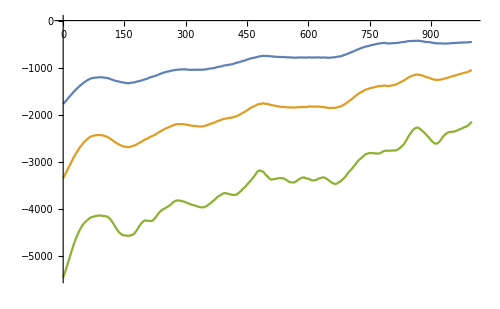

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]

ListLinePlot[fits]
```

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-